```mathematica
Quit[]
```

### Settings

```mathematica
SetDirectory[NotebookDirectory[]];
<<PlotOption`
```

```mathematica
NmapFileName="Nmap";
CompFileName="compaction";
LogwFileName="logw";
AnimationDirName="animation/";
HFileName="H";
piFileName="pi";
```

## Lattice (USR)

```mathematica
fileNumber="64_0";
DirName="data/USR/";
```

### BG

```mathematica
H[x_,p_]:=√(1/3(p^2/2+V[x]))
```

```mathematica
ϵH[x_,p_]:=p^2/(2 H[x,p]^2);
```

```mathematica
ηH[x_,p_]:=-(-3H[x,p]p-Vp[x])/(H[x,p]p);
```

```mathematica
para={𝒫IR->85 10^-11,Λ->17 10^2,H0->10^-5};
```

```mathematica
H0=10^-5;
```

```mathematica
V0=3 H0^2;
```

```mathematica
τ0=-1;
```

```mathematica
Ap=√((9 H0^6)/(4 π^2 𝒫IR))/.para;Am=Ap/Λ/.para;a0=-1/(τ0 H0);
```

```mathematica
Am0=0 Ap/Λ^2/.para;
```

```mathematica
range=-180356 10^-7;
```

```mathematica
V[x_]:=Piecewise[{{V0+Ap x,x>0},{V0+Am0 x,range<x<=0},{V0+Am x,x<=range}}]
Vp[x_]:=Piecewise[{{Ap,x>0},{Am0,range<x<=0},{Am,x<=range}}]
```

```mathematica
xi=193 10^-4;pi=-545 10^-9;Hi=H[xi,pi];ti=0;tf=10 Hi^-1;
```

```mathematica
solb=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+Vp[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[ti]==xi,dϕ[ti]==pi,NN[ti]==0},{ϕ[t],dϕ[t],NN[t]},{t,ti,tf},MaxSteps->Infinity,WorkingPrecision->50][[1]];
```

```mathematica
Φsol[t_]=ϕ[t]/.solb;
dΦsol[t_]=dϕ[t]/.solb;
Nsol[t_]=NN[t]/.solb;
Hsol[t_]=H[Φsol[t],dΦsol[t]];
ϵHsol[t_]=ϵH[Φsol[t],dΦsol[t]];
ηHsol[t_]=ηH[Φsol[t],dΦsol[t]];
```

```mathematica
dH[t_]=Hsol'[t];ddH[t_]=Hsol''[t];
```

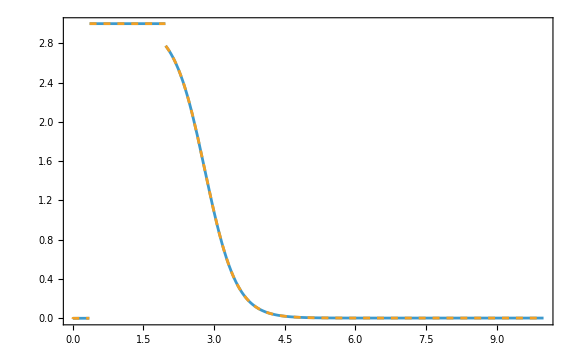

```mathematica
ParametricPlot[{{Nsol[t],ηHsol[t]},{Nsol[t],-ddH[t]/(2Hsol[t]dH[t])}},{t,ti,tf}(*,ScalingFunctions->{Identity,"Log"}*),PlotRange->All,PlotStyle->{{},{Dashed}}]
```

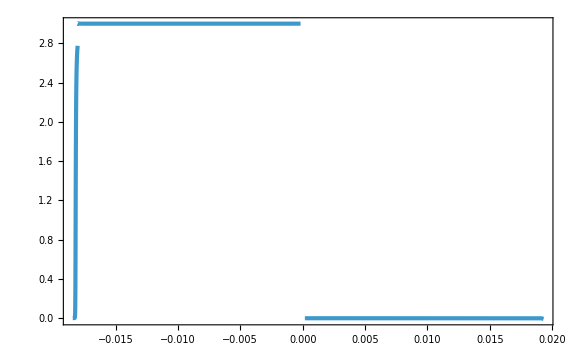

```mathematica
ParametricPlot[{Φsol[t],-ddH[t]/(2Hsol[t]dH[t])},{t,ti,tf},PlotRange->All]
```

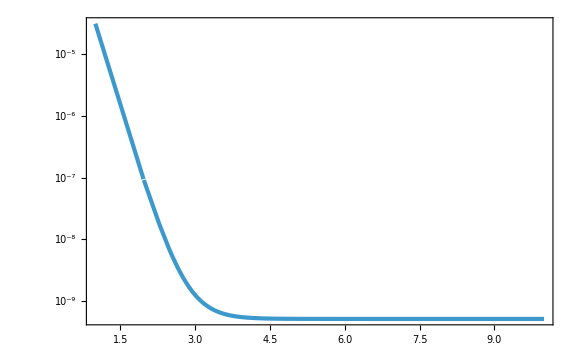

```mathematica
ParametricPlot[{Nsol[t],ϵHsol[t]},{t,ti+1 Hi^-1,tf},ScalingFunctions->{Identity,"Log"},PlotRange->All]
```

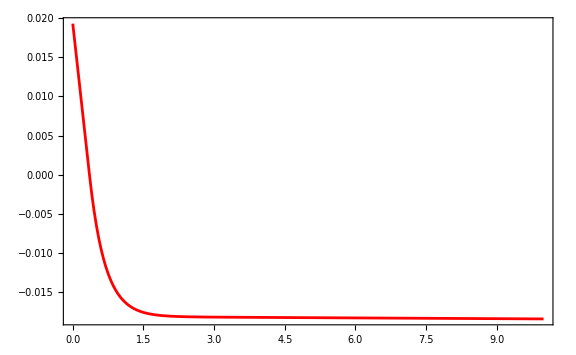

```mathematica
Figphi=ParametricPlot[{Nsol[t],Φsol[t]},{t,ti(*+11 Hi^-1*),tf},PlotRange->All,PlotStyle->{Red},PlotPoints->200]
```

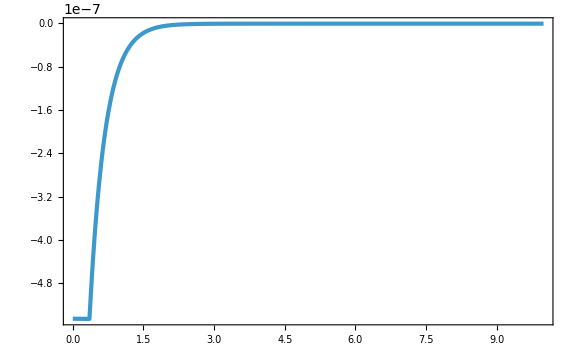

```mathematica
ParametricPlot[{Nsol[t],dΦsol[t]},{t,ti(*+11 Hi^-1*),tf},PlotRange->All]
```

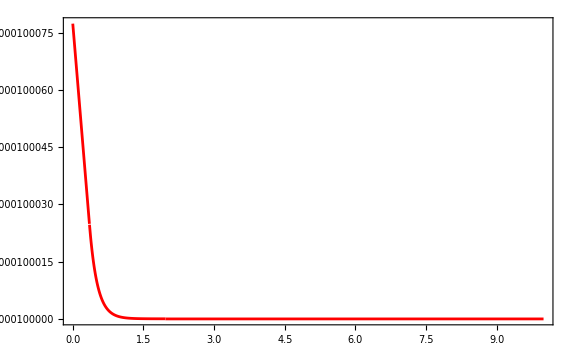

```mathematica
FigH=ParametricPlot[{{Nsol[t],Hsol[t]}},{t,ti,tf}(*,ScalingFunctions->{Identity,"Log"}*),PlotRange->All,PlotStyle->{Red},PlotPoints->200]
```

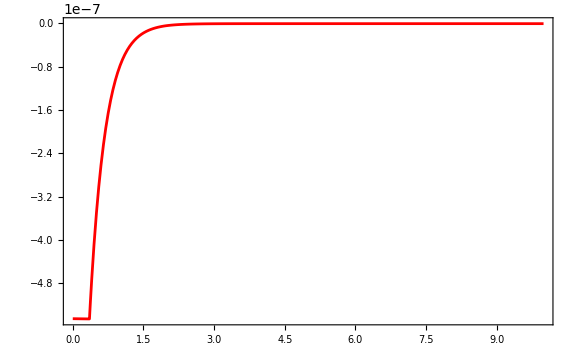

```mathematica
Figpi=ParametricPlot[{{Nsol[t],dΦsol[t]}},{t,ti,tf}(*,ScalingFunctions->{Identity,"Log"}*),PlotRange->All,PlotStyle->{Red},PlotPoints->200]
```

### Curvature perturbation PDF

```mathematica
NfileName=DirName<>NmapFileName<>"_"<>fileNumber<>".dat";
```

```mathematica
NMap=Map[#[[2]]&,Sort[Import[NfileName]]];
```

```mathematica
num=Length[NMap]^(1/3)
```

64

```mathematica
NMean=Mean[NMap]
```

23.6381

```mathematica
NVari=Variance[NMap]
```

0.0372947

```mathematica
Skewness[NMap]
Kurtosis[NMap]
```

0.201038

2.86626

```mathematica
MinN=Min[NMap]-NMean;MaxN=Max[NMap]-NMean;
```

```mathematica
HistList=HistogramList[NMap-NMean,20,"PDF"];
HistTable=Table[{(HistList[[1,ii]]+HistList[[1,ii+1]])/2,HistList[[2,ii]]},{ii,1,Length[HistList[[2]]]}];
```

```mathematica
exptail[t_,σ_,β_]:=ⅇ^(-β t)/(√(2π σ^2))Exp[-1/(2 σ^2)(1/β(1-ⅇ^(-β t)))^2]
fit=FindFit[HistTable,exptail[t,σ,β],{σ,β},t,WorkingPrecision->40]
```

{σ→-0.2002457099507379771991719668066234233032,β→0.2034881149968768166911513089648417108924}

```mathematica
FitFunc[t_,γ_,δ_,μ_,σ_]:=PDF[JohnsonDistribution["SU",γ,δ,μ,σ],t]
fitF=FindFit[HistTable,FitFunc[t,γ,δ,μ,σ],{γ,δ,μ,σ},t,WorkingPrecision->30,MaxIterations->1000]
```

FindFit::cvmit: 1000回以内の反復では要求された精度または確度に収束することができませんでした．

{γ→-103.610032119848070380184792573,δ→38.7720951703558301009950333218,μ→-7.67890914661128026841396715586,σ→1.06534221993173466815877773006}

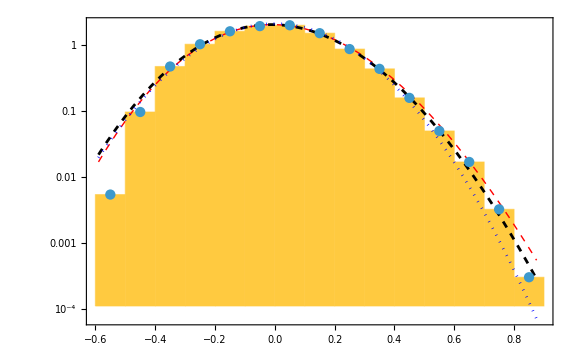

```mathematica
Show[Histogram[NMap-NMean,20,"PDF",ScalingFunctions->"Log"],
LogPlot[exptail[t,σ,β]/.fit,{t,MinN,MaxN},PlotStyle->{Dashed,Red,Thick}],
LogPlot[FitFunc[t,γ,δ,μ,σ]/.fitF,{t,MinN,MaxN},PlotStyle->{Dashed,Black}],
LogPlot[1/Sqrt[2π σ2] Exp[-x^2/(2σ2)]/.{σ2->Variance[NMap]},{x,MinN,MaxN},PlotStyle->{Dotted,Blue}],
ListLogPlot[HistTable,Joined->False]]
```

### Curvature perturbation Map

```mathematica
zeta0=ArrayReshape[NMap-NMean,{num,num,num}];
shift=First@Position[zeta0,Max[zeta0]]-num/2;
zeta=RotateLeft[zeta0,shift];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta//Flatten]]
```

0.579355

```mathematica
First@Position[zeta,Max[zeta]]
```

{32,32,32}

```mathematica
ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
ListPlot3D[zeta[[num/2]],PlotRange->All,BoxRatios->{1, 1, 0.4},Ticks->None,ColorFunction->"Rainbow",PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta+0.1}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]]]
```

-Graphics3D-

### Compaction

```mathematica
CfileName=DirName<>CompFileName<>"_"<>fileNumber<>".dat";
LfileName=DirName<>LogwFileName<>"_"<>fileNumber<>".dat";
```

```mathematica
dr=1;
```

```mathematica
zetardata[r_]:=Select[Flatten[Table[If[Abs[√((nx-num/2)^2+(ny-num/2)^2+(nz-num/2)^2)-r]<=dr/2,zeta[[nx,ny,nz]],None],{nx,1,num},{ny,1,num},{nz,1,num}],2],NumberQ]
```

```mathematica
AbsoluteTiming[zetarList=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>1,{r,Mean[zetardatas]±StandardDeviation[zetardatas]/Sqrt[Length[zetardatas]]},None],{r,0,num/2-1,dr}],Length[#]>1&];]
```

{50.8624,Null}

```mathematica
AbsoluteTiming[zetarListwoError=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>=1,{r,Mean[zetardatas]},None],{r,0,num/2-1}],Length[#]>=1&];]
```

{52.6232,Null}

```mathematica
Beep[]
```

```mathematica
zetarList=Join[{zetarListwoError[[1]]},zetarList];
```

```mathematica
Nbias=3.0;
```

```mathematica
ksigma[NN_]=(2π σ E^NN)/num/.{σ->10^-1};
```

```mathematica
fit=FindFit[Drop[zetarListwoError,1],A Sinc[ksigma[Nbias]r],A,r]
```

{A→0.643017}

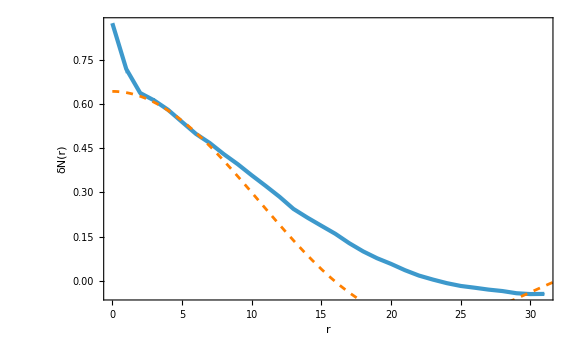

```mathematica
Show[ListPlot[zetarList,FrameLabel->{r,"δN(r)"},PlotLegends->Placed[LineLegend[{"lattice"},LegendMarkerSize->30],{0.8,0.8}](*,PlotRange->{-0.5,5A/.fit}*)],Plot[A Sin[ksigma[Nbias]r]/(ksigma[Nbias]r)/.fit,{r,0,num/2},PlotStyle->{Orange,Dashed},PlotLegends->Placed[LineLegend[{"(sin (SubscriptBox[k, σ] r))/k_σ"},LegendMarkerSize->30],{0.8,0.8}],PlotRange->All]]
```

```mathematica
zetarint[r_]=Interpolation[zetarListwoError][r];
```

```mathematica
dzeta=Join[{0},Table[(zetarListwoError[[ii+2,2]]-zetarListwoError[[ii,2]])/2,{ii,1,num/2-2}],{0}];
```

```mathematica
CompactionC[r_]=2/3(1-(1+r zetarint'[r])^2);
CompactionD[r_]=2/3(1-(1+r dzeta[[r+1]])^2);//Quiet
```

```mathematica
CDList=Table[{r,CompactionD[r]},{r,0,num/2-1}];
```

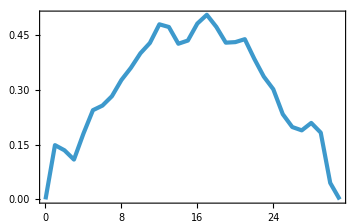

```mathematica
ListPlot[CDList,ImageSize->Medium]
```

```mathematica
CList=Table[{(*ksigma[Nbias]*)r,CompactionC[r]},{r,0,num/2-1}];
```

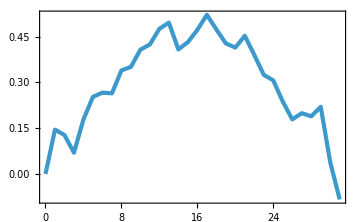

```mathematica
ListPlot[CList,ImageSize->Medium]
```

```mathematica
CompList=Import[CfileName];
```

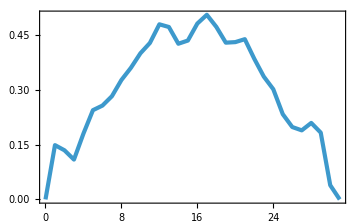

```mathematica
ListPlot[CompList,ImageSize->Medium]
```

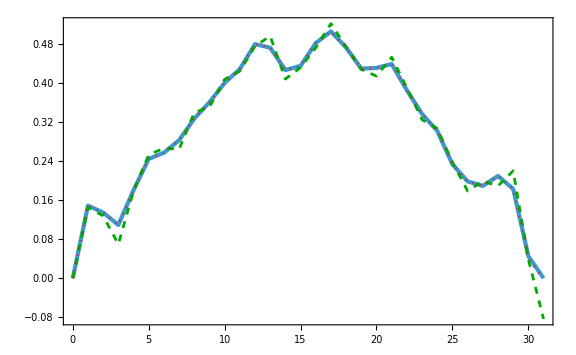

```mathematica
Show[ListPlot[CDList],
ListPlot[CList,PlotStyle->{Dashed,Darker[Green]}],
ListPlot[CompList,PlotStyle->{Dotted,Red}],PlotRange->All]
```

```mathematica
CompactionMax=FindMaximum[{CompactionC[r],0<r<num/2-1},{r,num/2-3}];
```

```mathematica
CmpMax=CompactionMax[[1]]
rmax=r/.CompactionMax[[2]]
```

0.52429

16.757

```mathematica
Rmax=rmax Exp[zetarint[rmax]]
```

19.1886

```mathematica
NIntegrate[r^2 CompactionC[r] Exp[3zetarint[r]](1+r zetarint'[r]),{r,0,rmax}]/(Rmax^3/3)
```

0.380926

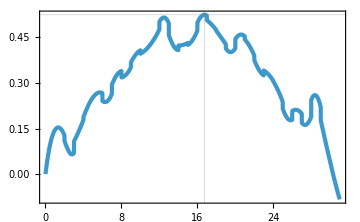

```mathematica
Plot[CompactionC[r],{r,0,num/2-1},GridLines->{{rmax},{CmpMax}},ImageSize->Medium]
```

```mathematica
(** Discretize **)
```

```mathematica
CDList2=Table[CDList[[r,2]],{r,1,num/2}];
```

```mathematica
CmpMaxD=Max[CDList2]
```

0.505623

```mathematica
rmaxD=Ordering[CDList2,-1][[1]]
```

18

```mathematica
RmaxD=(rmaxD-1) Exp[zetarListwoError[[rmaxD,2]]]
```

19.3171

```mathematica
Sum[(r-1)^2 CDList[[r,2]] Exp[3zetarListwoError[[r,2]]](1+(r-1) dzeta[[r]]),{r,1,rmaxD}]/(RmaxD^3/3)
```

0.408324

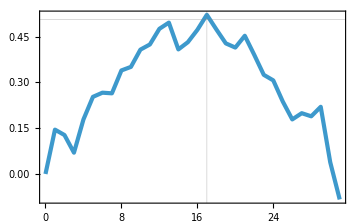

```mathematica
ListPlot[CList,GridLines->{{rmaxD-1},{CmpMaxD}},ImageSize->Medium]
```

### Averaged Power Spectrum

```mathematica
calPkdisc=Import["data/USR/powers.dat"];
```

```mathematica
calPave=Table[0,{ii,Length[Drop[calPkdisc[[1]],1]]}];
Do[calPave+=Drop[calPkdisc[[ii]],1],{ii,Length[calPkdisc]}]
```

```mathematica
cn=0.1;
logn[i_]=(i-1)*cn;
```

```mathematica
calPkAve=Table[{Exp[logn[i]],calPave[[i]]/Length[calPkdisc]},{i,Length[Drop[calPkdisc[[1]],1]]}];
```

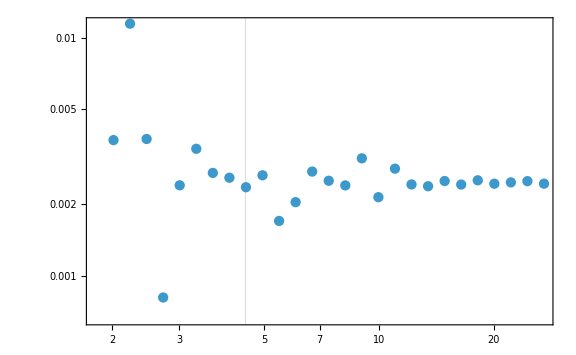

```mathematica
ListLogLogPlot[calPkAve[[8;;Length[calPkAve]-1]],Joined->False,GridLines->{{0.1 ⅇ^3.8},None},PlotRange->All]
```

```mathematica
𝒫Rnum[κ_]:=𝒫IR((9(Λ-1)^2)/κ^6(Sin[κ]-κ Cos[κ])^4+(Λ+(3(Λ-1))/(2 κ^3)((κ^2-1)Sin[2κ]+2κ Cos[2κ]))^2)
```

```mathematica
kmax=k/.FindRoot[𝒫Rnum[k]==10^-1 ⅇ^(38/10)/.para,{k,3},WorkingPrecision->30]//Quiet
```

3.13988712748113282849723315377

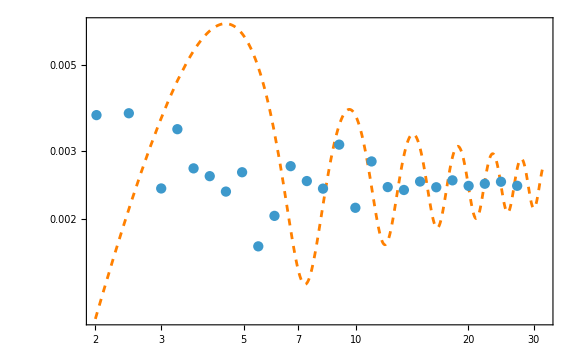

```mathematica
Show[LogLogPlot[𝒫Rnum[kmax/(0.1 ⅇ^3.8) nn]/.para,{nn,2,32},PlotStyle->{Dashed,Orange}],ListLogLogPlot[calPkAve[[8;;Length[calPkAve]-1]],Joined->False,GridLines->{{0.1 ⅇ^3.8},None},PlotRange->All]]
```

### Animation

```mathematica
AbsoluteTiming[HMapData=Import[DirName<>AnimationDirName<>HFileName<>"_"<>fileNumber<>".dat"];
piMapData=Import[DirName<>AnimationDirName<>piFileName<>"_"<>fileNumber<>".dat"];]
```

{13.1152,Null}

```mathematica
num=Length[First[HMapData]]^(1/3)
```

64

```mathematica
efoldLength=Length[HMapData]
```

58

```mathematica
HMeanList=Table[Mean[HMapData[[efoldN]]],{efoldN,Length[HMapData]}];//AbsoluteTiming
piMeanList=Table[Mean[piMapData[[efoldN]]],{efoldN,Length[piMapData]}];//AbsoluteTiming
```

{0.070387,Null}

{0.068671,Null}

```mathematica
(*Table[Variance[HMapData[[efoldN]]],{efoldN,Length[HMapData]}]*)
```

```mathematica
(*Table[Variance[piMapData[[efoldN]]],{efoldN,Length[HMapData]}]*)
```

```mathematica
zetamap[efoldN_]:=Table[(HMapData[[efoldN,num^2 (nx-1)+num(ny-1)+nz]]-HMeanList[[efoldN]])/piMeanList[[efoldN]],{nx,num},{ny,num},{nz,num}]
```

```mathematica
Dzeta=3Sqrt[Variance[zetamap[efoldLength]//Flatten]];
```

```mathematica
ListDensityPlot3D[RotateLeft[zetamap[37],shift],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Medium]
```

-Graphics3D-

```mathematica
zetaPlotList=Table[ListDensityPlot3D[RotateLeft[zetamap[i],shift],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(i-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large],{i,efoldLength}];//AbsoluteTiming
```

{19.7905,Null}

```mathematica
Export["data/USR/fig/zetat_"<>fileNumber<>".gif",zetaPlotList];//AbsoluteTiming
```

{10.8373,Null}

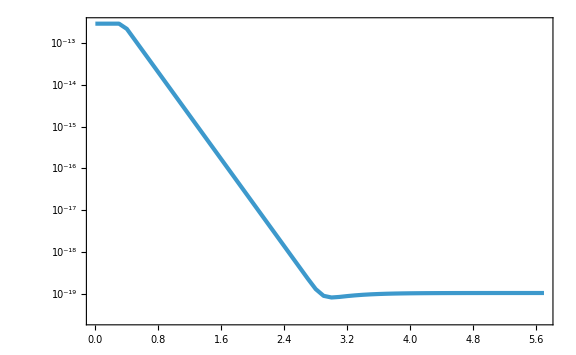

```mathematica
ListLogPlot[Table[{0.1(i-1),piMeanList[[i]]},{i,efoldLength}]]
```

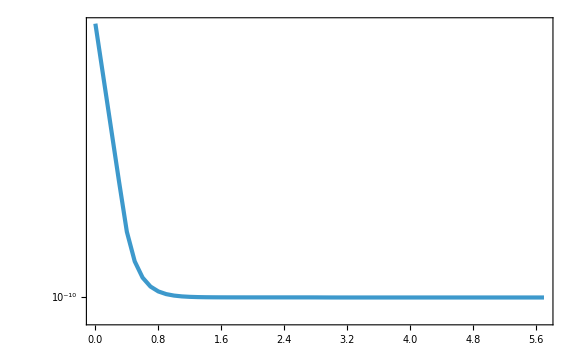

```mathematica
ListLogPlot[Table[{0.1(i-1),HMeanList[[i]]},{i,efoldLength}]]
```

```mathematica
(*Show[Figphi,ListPlot[Table[{0.1(i-1),piMeanList[[i]]},{i,efoldLength}],Joined->False],PlotRange->{{0.1,4},{-0.019,0}}]*)
```

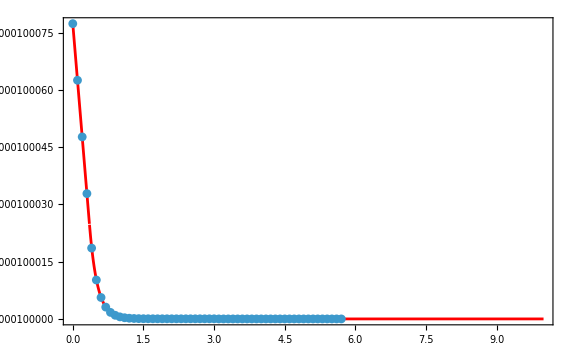

```mathematica
Show[FigH,ListPlot[Table[{0.1(i-1),HMapData[[i,1+0Length[HMapData[[1]]]]]},{i,efoldLength}],Joined->False],PlotRange->All]
```

## Lattice (Starobinsky)

### Animation

```mathematica
AbsoluteTiming[HMapData=Import["STOLAS_single/data/Starobinsky/animation/H_64_0.dat"];
piMapData=Import["STOLAS_single/data/Starobinsky/animation/pi_64_0.dat"];]
```

{13.4474,Null}

```mathematica
num=Length[First[HMapData]]^(1/3)
```

64

```mathematica
Length[HMapData]
```

57

```mathematica
HMeanList=Table[Mean[HMapData[[efoldN]]],{efoldN,Length[HMapData]}];//AbsoluteTiming
piMeanList=Table[Mean[piMapData[[efoldN]]],{efoldN,Length[piMapData]}];//AbsoluteTiming
```

{0.07135,Null}

{0.069618,Null}

```mathematica
zetaList=ParallelTable[(HMapData[[efoldN,num^2 (nx-1)+num(ny-1)+nz]]-HMeanList[[efoldN]])/piMeanList[[efoldN]],{efoldN,1,Length[HMapData],5},{nx,num},{ny,num},{nz,num}];//AbsoluteTiming
```

{666.566,Null}

```mathematica
Length[HMapData]
```

57

```mathematica
Dzeta=3Sqrt[Variance[Last[zetaList]//Flatten]]
```

Flatten::normal: Flatten[IterationLimit]で1の位置に原子的ではない式が想定されます．

3 √Variance[Flatten[IterationLimit]]

```mathematica
zetaPlotList=Table[ListDensityPlot3D[zetaList[[i]],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(i-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large],{i,Length[zetaList]}];//AbsoluteTiming
```

{1.01673,Null}

```mathematica
Export["STOLAS_single/data/Starobinsky/zetat_64_640.gif",zetaPlotList];//AbsoluteTiming
```

{8.73108,Null}

```mathematica
Last[zetaPlotList]
```

-Graphics3D-

```mathematica
Beep[]
```

```mathematica
(*zetamap=ParallelTable[(HMapData[[57,num^2 (nx-1)+num(ny-1)+nz]]-HMeanList[[57]])/piMeanList[[57]],{nx,num},{ny,num},{nz,num}];*)
```

```mathematica
(*Dzeta=3Sqrt[Variance[zetamap//Flatten]]*)
```

```mathematica
(*ListDensityPlot3D[zetamap,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(57-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large]*)
```

### Curvature perturbation PDF

```mathematica
fileNumber="256_0";
DirName="data/Starobinsky/";
NmapFileName="Nmap";
CompFileName="compaction";
LogwFileName="logw";
NfileName=DirName<>NmapFileName<>"_"<>fileNumber<>".dat";
CfileName=DirName<>CompFileName<>"_"<>fileNumber<>".dat";
LfileName=DirName<>LogwFileName<>"_"<>fileNumber<>".dat";
```

```mathematica
NMap=Map[#[[2]]&,Sort[Import[NfileName]]];
```

```mathematica
num=Length[NMap]^(1/3)
```

256

```mathematica
NMean=Mean[NMap]
```

21.1205

```mathematica
NVari=Variance[NMap]
```

0.0126921

```mathematica
Skewness[NMap]
Kurtosis[NMap]
```

-0.0270813

2.97808

```mathematica
dN=10 10^-2;
```

```mathematica
histNMap[zz_]:=Select[Flatten[Table[If[zz≤NMap[[cc]]-NMean<zz+dN,NMap[[cc]]-NMean,None],{cc,1,num^3}],2],NumberQ]
```

```mathematica
(*NMapHistList=Select[Table[Ndatas=histNMap[r];If[Length[Ndatas]≥1,{r+dN/2,Length[Ndatas]/(num^3 dN)},None],{r,-5/5,5/5,dN}],Length[#]>1&];*)
```

```mathematica
(*Show[ListLogPlot[NMapHistList,Joined->False],LogPlot[1/Sqrt[2π σ2] Exp[-x^2/(2σ2)]/.{σ2->Variance[NMap]},{x,-1,1}],PlotRange->All]*)
```

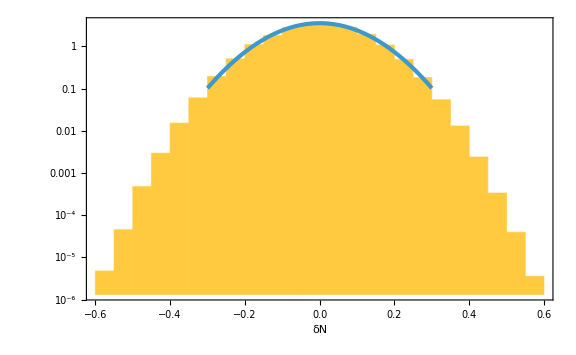

```mathematica
Show[Histogram[NMap-NMean,20,"PDF",ScalingFunctions->"Log",FrameLabel->{"δN",None}],
LogPlot[1/Sqrt[2π σ2] Exp[-x^2/(2σ2)]/.{σ2->Variance[NMap]},{x,-0.3,00.3}](*,
ListLogPlot[NMapHistList,Joined->False,PlotStyle->Red]*),
PlotRange->All]
```

```mathematica
zeta2=Table[If[nx<0,nxt=nx+num,nxt=nx];If[ny<0,nyt=ny+num,nyt=ny];If[nz<0,nzt=nz+num,nzt=nz];NMap[[num^2 nxt+num nyt+nzt+1]]-NMean,{nx,-num/2+1,num/2},{ny,-num/2+1,num/2},{nz,-num/2+1,num/2}];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta2//Flatten]]
```

0.337978

```mathematica
dNFig=ListDensityPlot3D[zeta2,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

```mathematica
ListPlot3D[zeta2[[num/2]],PlotRange->All,BoxRatios->{1, 1, 0.4},Ticks->None,ColorFunction->"Rainbow",PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta+0.1}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

### Compaction

```mathematica
fileNumber="32_0";
DirName="data/Starobinsky/";
NmapFileName="Nmap";
CompFileName="compaction";
LogwFileName="logw";
NfileName=DirName<>NmapFileName<>"_"<>fileNumber<>".dat";
CfileName=DirName<>CompFileName<>"_"<>fileNumber<>".dat";
LfileName=DirName<>LogwFileName<>"_"<>fileNumber<>".dat";
```

```mathematica
NMap=Map[#[[2]]&,Sort[Import[NfileName]]];
```

```mathematica
num=Length[NMap]^(1/3)
```

32

```mathematica
NMean=Mean[NMap]
```

21.1257

```mathematica
zeta=Table[NMap[[num^2 (nx-1)+num(ny-1)+nz]]-NMean,{nx,num},{ny,num},{nz,num}];
```

```mathematica
zeta2=Table[If[nx<0,nxt=nx+num,nxt=nx];If[ny<0,nyt=ny+num,nyt=ny];If[nz<0,nzt=nz+num,nzt=nz];NMap[[num^2 nxt+num nyt+nzt+1]]-NMean,{nx,-num/2+1,num/2},{ny,-num/2+1,num/2},{nz,-num/2+1,num/2}];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta//Flatten]]
```

0.340959

```mathematica
(*ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large];*)
```

```mathematica
dNFig=ListDensityPlot3D[zeta2,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
ListPlot3D[zeta2[[num/2+5]],BoxRatios->{1, 1, 0.4},PlotRange->All,Ticks->None,ColorFunction->"Rainbow",PlotLegends->BarLegend[{Automatic,{Min[zeta2],Max[zeta2]}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
(*Export["chaotic/zeta_32_4.pdf",dNFig];*)
```

```mathematica
dr=1;
Clear[zetardata(*,nxt,nyt,nzt*)]
(*zetardata[r_]:=Select[Flatten[Table[If[(Max[r-dr/2,0])^2<=(i-1)^2+(j-1)^2+(k-1)^2<(r+dr/2)^2,zeta2[[i,j,k]],None],{i,num/2},{j,num/2},{k,num/2}],2],NumberQ]*)
```

```mathematica
zetardata[r_]:=Select[Flatten[Table[If[nx<0,nxt=nx+num,nxt=nx];
If[ny<0,nyt=ny+num,nyt=ny];
If[nz<0,nzt=nz+num,nzt=nz];If[Abs[√(nx^2+ny^2+nz^2)-r]<=dr/2,zeta[[nxt+1,nyt+1,nzt+1]],None],{nx,-num/2+1,num/2},{ny,-num/2+1,num/2},{nz,-num/2+1,num/2}],2],NumberQ]
```

```mathematica
zetarList=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>1,{r,Mean[zetardatas]±StandardDeviation[zetardatas]/Sqrt[Length[zetardatas]]},None],{r,0,num/2-1,dr}],Length[#]>1&];
zetarListwoError=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>=1,{r,Mean[zetardatas]},None],{r,0,num/2-1}],Length[#]>=1&];
```

```mathematica
zetarList=Join[{zetarListwoError[[1]]},zetarList];
```

```mathematica
Nbias=3.8;
```

```mathematica
ksigma[NN_]=(2π σ E^NN)/num/.{σ->10^-1};
```

```mathematica
fit=FindFit[Drop[zetarListwoError,1],A Sin[ksigma[Nbias]r]/(ksigma[Nbias]r),A,r]
```

{A→-0.0961598}

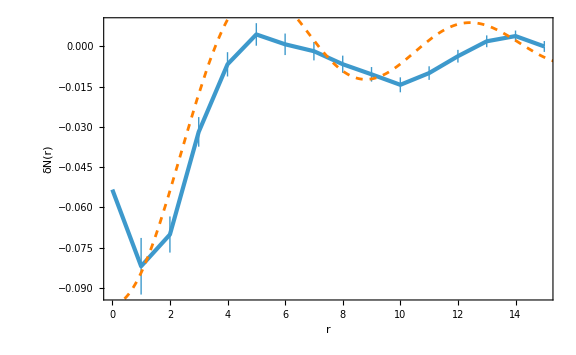

```mathematica
Show[ListPlot[zetarList,FrameLabel->{r,"δN(r)"},PlotLegends->Placed[LineLegend[{"lattice"},LegendMarkerSize->30],{0.8,0.8}](*,PlotRange->{-0.5,5A/.fit}*)],Plot[A Sin[ksigma[Nbias]r]/(ksigma[Nbias]r)/.fit,{r,0,num/2},PlotStyle->{Orange,Dashed},PlotLegends->Placed[LineLegend[{"(sin (SubscriptBox[k, σ] r))/k_σ"},LegendMarkerSize->30],{0.8,0.8}],PlotRange->Full]]
```

```mathematica
zetarint[r_]=Interpolation[zetarListwoError][r];
```

```mathematica
(*dzeta=Join[Table[(zetarListwoError[[ii+2,2]]-zetarListwoError[[ii,2]])/2,{ii,1,num/2-2}],{0}];*)dzeta=Join[{0},Table[(zetarListwoError[[ii+2,2]]-zetarListwoError[[ii,2]])/2,{ii,1,num/2-2}],{0}];
```

```mathematica
CompactionC[r_]=2/3(1-(1+r zetarint'[r])^2);
CompactionD[r_]=2/3(1-(1+r dzeta[[r+1]])^2);//Quiet
```

```mathematica
CDList=Table[{r,CompactionD[r]},{r,0,num/2-1}];
```

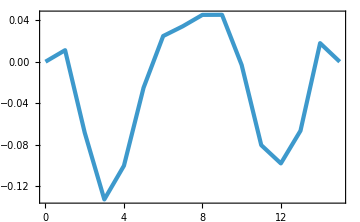

```mathematica
ListPlot[CDList,ImageSize->Medium]
```

```mathematica
CList=Table[{(*ksigma[Nbias]*)r,CompactionC[r]},{r,0,num/2-1}];
```

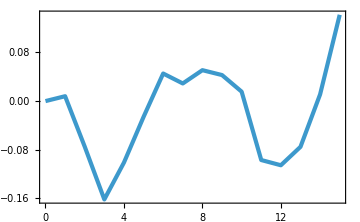

```mathematica
ListPlot[CList,ImageSize->Medium]
```

```mathematica
CompList=Import[CfileName];
```

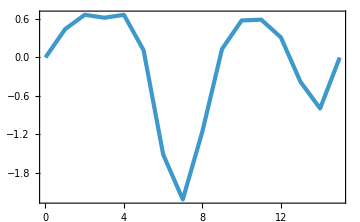

```mathematica
ListPlot[CompList,ImageSize->Medium]
```

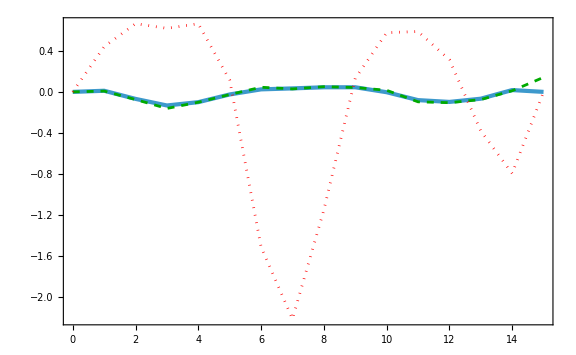

```mathematica
Show[ListPlot[CDList],
ListPlot[CList,PlotStyle->{Dashed,Darker[Green]}],
ListPlot[CompList,PlotStyle->{Dotted,Red}],PlotRange->All]
```

```mathematica
{{0,0},{1,0.4421908531},{2,0.6666422907},{3,0.6210110452},{4,0.6657194876},{5,0.1143851654},{6,-1.515480482},{7,-2.217920522},{8,-1.153908079},{9,0.1316328082},{10,0.5782360351},{11,0.5902348917},{12,0.3141946655},{13,-0.3806311373},{14,-0.7966779529},{15,0}}-CompList
```

{{0,0},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0.},{0,0}}

```mathematica
(* Continuous averaged compaction function*)
```

```mathematica
CompactionMax=FindMaximum[{CompactionC[r],0<r<num/2-1},{r,num/2-3}];
```

InterpolatingFunction::dmval: 入力値{15.0006}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{15.0007}は補間関数のデータ範囲外です．外挿が使用されます．

InterpolatingFunction::dmval: 入力値{15.0001}は補間関数のデータ範囲外です．外挿が使用されます．

General::stop: この計算中に，InterpolatingFunction::dmvalのこれ以上の出力は表示されません．

```mathematica
CmpMax=CompactionMax[[1]]
rmax=r/.CompactionMax[[2]]
```

0.141925

15.

```mathematica
Rmax=rmax Exp[zetarint[rmax]]
```

14.9986

```mathematica
NIntegrate[r^2 CompactionC[r] Exp[3zetarint[r]](1+r zetarint'[r]),{r,0,rmax}]/(Rmax^3/3)
```

-0.0191894

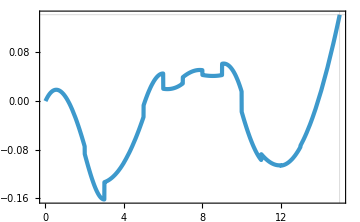

```mathematica
Plot[CompactionC[r],{r,0,num/2-1},GridLines->{{rmax},{CmpMax}},ImageSize->Medium]
```

```mathematica
(** Discretize **)
```

```mathematica
CDList2=Table[CDList[[r,2]],{r,1,num/2}];
```

```mathematica
CmpMaxD=Max[CDList2]
```

0.0451871

```mathematica
rmaxD=Ordering[CDList2,-1][[1]]
```

10

```mathematica
RmaxD=(rmaxD-1) Exp[zetarListwoError[[rmaxD,2]]]
```

8.90639

```mathematica
Sum[(r-1)^2 CDList[[r,2]] Exp[3zetarListwoError[[r,2]]](1+(r-1) dzeta[[r]]),{r,1,rmaxD}]/(RmaxD^3/3)
```

0.0208411

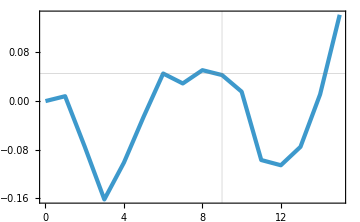

```mathematica
ListPlot[CList,GridLines->{{rmaxD-1},{CmpMaxD}},ImageSize->Medium]
```

### Averaged Power Spectrum

```mathematica
calPkdisc=Import["data/Starobinsky/powers.dat"];
```

```mathematica
calPave=Table[0,{ii,Length[Drop[calPkdisc[[1]],1]]}];
Do[calPave+=Drop[calPkdisc[[ii]],1],{ii,Length[calPkdisc]}]
```

```mathematica
cn=0.1;
logn[i_]=(i-1)*cn;
```

```mathematica
calPkAve=Table[{Exp[logn[i]],calPave[[i]]/Length[calPkdisc]},{i,Length[Drop[calPkdisc[[1]],1]]}];
```

```mathematica
kmax=k/.FindRoot[𝒫Rnum[k]==10^-1 ⅇ^(38/10)/.para,{k,3},WorkingPrecision->30]//Quiet
```

3.13988712748113282849723315377

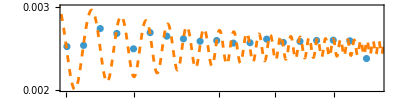

```mathematica
Show[ListLogLogPlot[calPkAve,Joined->False,GridLines->{{0.1 ⅇ^3.8},None},PlotRange->{{20,130},{2 10^-3,3 10^-3}},AspectRatio->1/4,ImageSize->Full],LogLogPlot[𝒫Rnum[kmax/(0.1 ⅇ^3.8) nn]/.para,{nn,1,150},PlotStyle->{Dashed,Orange}]]
```

### PDF

```mathematica
DirName="Starobinsky/data/";
```

```mathematica
PDFFileName1=DirName<>"probabilities1.dat";
PDFFileName2=DirName<>"probabilities2.dat";
PDFFileName3=DirName<>"probabilities3.dat";
PDFFileName4=DirName<>"probabilities4.dat";
PDFFileName5=DirName<>"probabilities5.dat";
PDFFileName6=DirName<>"probabilities6.dat";
PDFFileName7=DirName<>"probabilities7.dat";
PDFFileName8=DirName<>"probabilities8.dat";
PDFFileName9=DirName<>"probabilities9.dat";
```

```mathematica
CompactionPDF=Join[Import[PDFFileName1],Import[PDFFileName2],Import[PDFFileName3],Import[PDFFileName4],Import[PDFFileName5],Import[PDFFileName6],Import[PDFFileName7],Import[PDFFileName8],Import[PDFFileName9]];
```

```mathematica
clength=Length[CompactionPDF]
```

10000

```mathematica
logw=Table[CompactionPDF[[ii,2]],{ii,1,clength}];
```

```mathematica
(*weight=Table[Exp[CompactionPDF[[ii,2]]],{ii,1,clength}];*)
```

```mathematica
Cint=Table[CompactionPDF[[ii,3]],{ii,1,clength}];
```

```mathematica
Rmax=Table[CompactionPDF[[ii,5]],{ii,1,clength}];
```

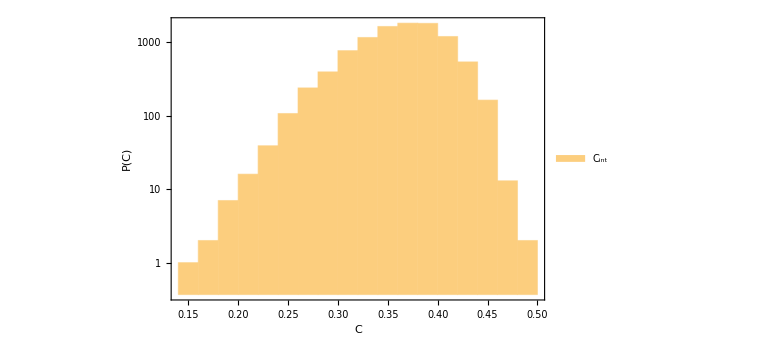

```mathematica
Show[Histogram[Cint,ScalingFunctions-> "Log",ChartLegends->{"C_int"}],PlotRange->All,Frame->True,FrameLabel->{"C","P(C)"}]
```

```mathematica
dc=1 10^-2;
```

```mathematica
histCintdata[c_]:=Select[Flatten[Table[If[c<Cint[[cc]]≤c+dc,Cint[[cc]],None],{cc,1,clength}],2],NumberQ]
```

```mathematica
(*histWintdata[c_]:=Select[Flatten[Table[If[c<Cint[[cc]]≤c+dc,weight[[cc]],None],{cc,1,clength}],2],NumberQ]*)
```

```mathematica
histlogwintdata[c_]:=Select[Flatten[Table[If[c<Cint[[cc]]≤c+dc,logw[[cc]],None],{cc,1,clength}],2],NumberQ]
```

```mathematica
CintListNW=Select[Table[cintdatas=histCintdata[r];(*weightdatas=histWintdata[r];*)If[Length[cintdatas]≥1,{r(*+dc/2*),Length[cintdatas]/(clength dc)},None],{r,0,60 10^-2,dc}],Length[#]>1&];
```

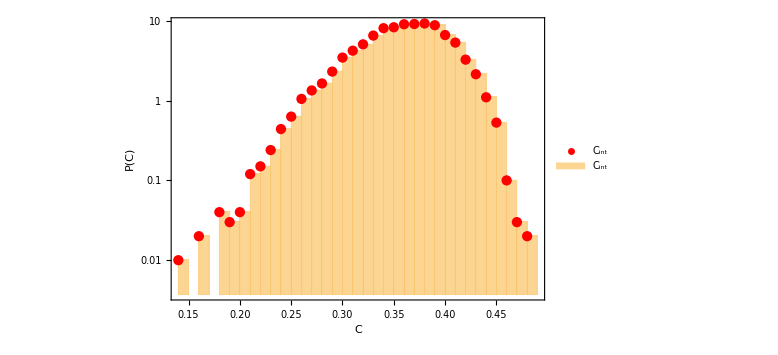

```mathematica
Show[Histogram[{Cint},40,"PDF",ScalingFunctions-> "Log",ChartLegends->{"C_int","C_max"}],ListLogPlot[CintListNW,Joined->False,PlotStyle->Red,PlotLegends->Placed[LineLegend[{"C_int"},LegendMarkerSize->30],{0.9,0.9}]],PlotRange->All,Frame->True,FrameLabel->{"C","P(C)"}]
```

```mathematica
CintList=Select[Table[cdatas=histCintdata[r];logwdatas=histlogwintdata[r];ProbC=Length[cdatas]/(clength dc)Exp[Mean[logwdatas]+Variance[logwdatas]/2];ϵpm[p_]:=Abs[Exp[(-1)^p √(Variance[logwdatas]/Length[cdatas]+Variance[logwdatas]^2/(2Length[cdatas]-2))]-1];If[Length[cdatas]>1,{r,Around[ProbC,{ProbC ϵpm[1],ProbC ϵpm[0]}]},None],{r,0,50 10^-2,dc}],Length[#]>1&];
```

Variance::shlen: 引数{}は少なくとも2つの要素を持っていなければなりません．

General::stop: この計算中に，Variance::shlenのこれ以上の出力は表示されません．

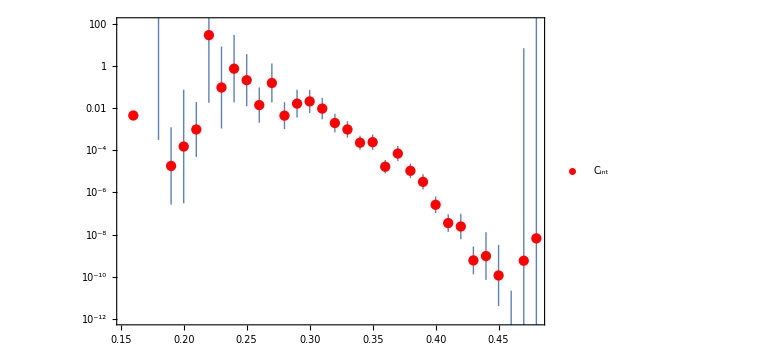

```mathematica
ListLogPlot[CintList,PlotRange->{Automatic,{10^-12,10^2}},GridLines->{{0.4},{10^-6}},Joined->False,PlotStyle->Red,PlotLegends->Placed[LineLegend[{"C_int"},LegendMarkerSize->30],{0.9,0.9}]]
```

```mathematica
WCbar=Table[{CompactionPDF[[ii,3]],Log10[Exp[CompactionPDF[[ii,2]]]]},{ii,1,clength}];
```

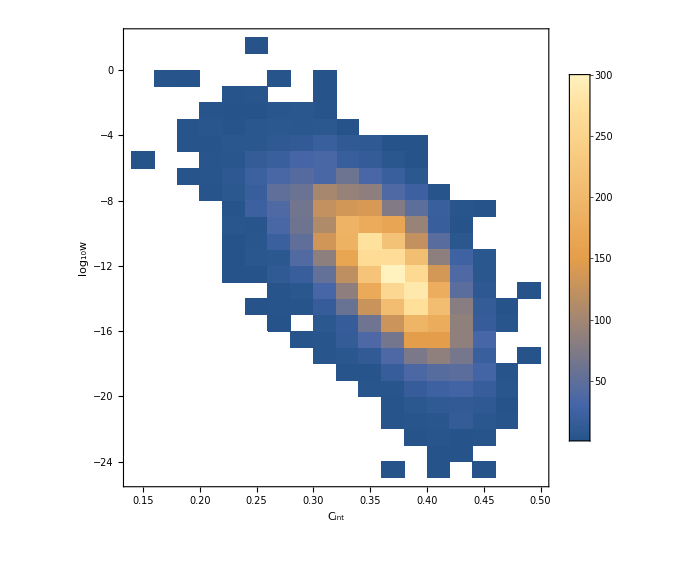

```mathematica
DensityHistogram[WCbar,20,FrameLabel->{"C_int","log_10w"},ChartLegends->Automatic,AspectRatio->1(*/GoldenRatio*)]
```

#### 𝒞Max

```mathematica
(*Cmax=Table[CompactionPDF[[ii,4]],{ii,1,clength}];*)
```

```mathematica
(*histCmaxdata[c_]:=Select[Flatten[Table[If[c<Cmax[[cc]]≤c+dc,Cmax[[cc]],None],{cc,1,clength}],2],NumberQ]*)
```

```mathematica
(*histWmaxdata[c_]:=Select[Flatten[Table[If[c<Cmax[[cc]]≤c+dc,weight[[cc]],None],{cc,1,clength}],2],NumberQ]*)
```

```mathematica
(*histlogwmaxdata[c_]:=Select[Flatten[Table[If[c<Cmax[[cc]]≤c+dc,logw[[cc]],None],{cc,1,clength}],2],NumberQ]*)
```

```mathematica
(*CmaxListNW=Select[Table[cmaxdatas=histCmaxdata[r];weightdatas=histWmaxdata[r];If[Length[cmaxdatas]>1,{r+dc,Length[cmaxdatas]/(clength dc)},None],{r,0,80 10^-2,dc}],Length[#]>1&];*)
```

```mathematica
(*ListLogPlot[CmaxListNW,Joined->False,PlotLegends->Placed[LineLegend[{"C_max"},LegendMarkerSize->30],{0.9,0.9}]]*)
```

```mathematica
(*CmaxList=Select[Table[cdatas=histCmaxdata[r];logwdatas=histlogwmaxdata[r];ProbC=Length[cdatas]/(clength dc)Exp[Mean[logwdatas]+Variance[logwdatas]/2];ϵpm[p_]:=Abs[Exp[(-1)^p √(StandardDeviation[logwdatas]^2/Length[cdatas]+StandardDeviation[logwdatas]^4/(2Length[cdatas]-2))]-1];If[Length[cdatas]>1,{r+dc,Around[ProbC,{ProbC ϵpm[1],ProbC ϵpm[0]}]},None],{r,0,80 10^-2,dc}],Length[#]>1&]//Quiet;*)
```

```mathematica
(*Show[ListLogPlot[CmaxList,Joined->False,PlotLegends->Placed[LineLegend[{"C_max"},LegendMarkerSize->30],{0.9,0.9}]]]*)
```

### Mass function

```mathematica
ParametersMass={K3->1,γ->36 10^-2,Cth->2/5,MassScale->10^20,HReentry->156 10^11 Mpc^-1};
```

```mathematica
LatticeSize=1/64 10^-12 Mpc;
```

```mathematica
PBHlist=Select[CompactionPDF,#[[3]]>Cth/.ParametersMass&];
```

```mathematica
PBHlength=Length[PBHlist]
```

1914

```mathematica
logwPBH=Table[PBHlist[[ii,2]],{ii,1,PBHlength}];
```

```mathematica
CintPBH=Table[PBHlist[[ii,3]],{ii,1,PBHlength}];
```

```mathematica
RmaxPBH=Table[PBHlist[[ii,5]],{ii,1,PBHlength}];
```

```mathematica
Mass[c_,r_]:=K3(c-Cth)^γ(MassScale(r^-1/HReentry)^-2)/.ParametersMass(** Kitajima, et al eq.(2.22) **)
```

```mathematica
PBHMass=Table[10^-20 Mass[CintPBH[[i]],LatticeSize RmaxPBH[[i]]],{i,PBHlength}]//Simplify;
```

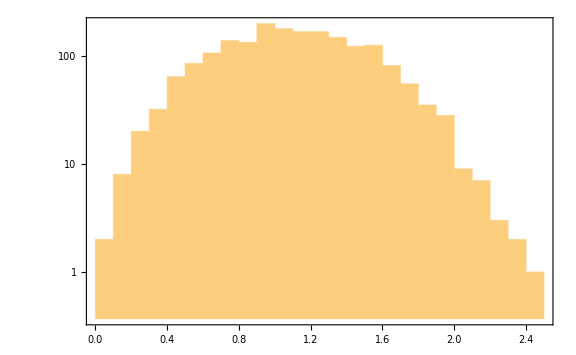

```mathematica
Histogram[PBHMass,ScalingFunctions->"Log"]
```

```mathematica
(*HistogramList[PBHMass]*)
```

```mathematica
dM=10 10^-2(*MassScale/.ParametersMass*);
```

```mathematica
MassList=Table[10^-1(1+dM)^cc,{cc,1,36}];MassList//N
```

{0.11,0.121,0.1331,0.14641,0.161051,0.177156,0.194872,0.214359,0.235795,0.259374,0.285312,0.313843,0.345227,0.37975,0.417725,0.459497,0.505447,0.555992,0.611591,0.67275,0.740025,0.814027,0.89543,0.984973,1.08347,1.19182,1.311,1.4421,1.58631,1.74494,1.91943,2.11138,2.32252,2.55477,2.81024,3.09127}

```mathematica
histMassPBH[MM_]:=Select[Flatten[Table[If[MM<PBHMass[[cc]]≤MM(1+dM),PBHMass[[cc]],None],{cc,1,PBHlength}],2],NumberQ]
```

```mathematica
histWintPBH[MM_]:=Select[Flatten[Table[If[MM<PBHMass[[cc]]≤MM(1+dM),logwPBH[[cc]],None],{cc,1,PBHlength}],2],NumberQ]
```

```mathematica
histRmaxPBH[MM_]:=Select[Flatten[Table[If[MM<PBHMass[[cc]]≤MM(1+dM),RmaxPBH[[cc]],None],{cc,1,PBHlength}],2],NumberQ]
```

```mathematica
CintPBHListNW=Select[Table[Massdatas=histMassPBH[MassList[[mm]]];ProbM=Length[Massdatas]/(clength (MassList[[mm+1]] -MassList[[mm]]));If[Length[Massdatas]≥1,{MassList[[mm]],ProbM},None],{mm,1,Length[MassList]-1}],Length[#]>1&];
```

```mathematica
CintPBHListNW//N
```

{{0.14641,0.0136603},{0.161051,0.00620921},{0.177156,0.0112895},{0.194872,0.0102632},{0.214359,0.00933015},{0.235795,0.0169639},{0.259374,0.0308435},{0.285312,0.0280395},{0.313843,0.00637262},{0.345227,0.0492429},{0.37975,0.0605662},{0.417725,0.0646359},{0.459497,0.0565836},{0.505447,0.0850732},{0.555992,0.0971237},{0.611591,0.10628},{0.67275,0.124861},{0.740025,0.132428},{0.814027,0.140044},{0.89543,0.179802},{0.984973,0.197975},{1.08347,0.156903},{1.19182,0.173684},{1.311,0.125095},{1.4421,0.135913},{1.58631,0.0762777},{1.74494,0.0378236},{1.91943,0.0192765},{2.11138,0.003789},{2.32252,0.0012917}}

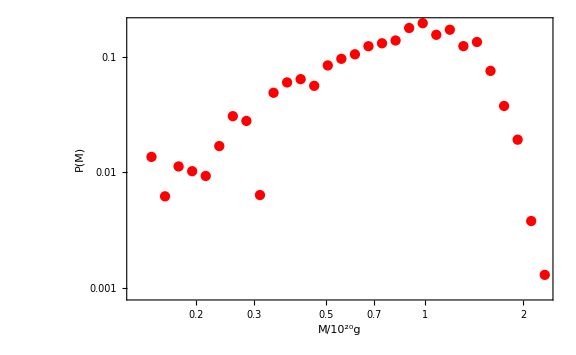

```mathematica
ListLogLogPlot[CintPBHListNW,Joined->False,PlotStyle->Red,FrameLabel->{"M/10^20g","P(M)"}]
```

```mathematica
MassPBHList=Select[Table[Massdatas=histMassPBH[MassList[[mm]]];logwdatas=histWintPBH[MassList[[mm]]];ProbC=Length[Massdatas]/(clength (MassList[[mm+1]] -MassList[[mm]]))Exp[Mean[logwdatas]+Variance[logwdatas]/2];ϵpm[p_]:=Abs[Exp[(-1)^p √(StandardDeviation[logwdatas]^2/Length[Massdatas]+StandardDeviation[logwdatas]^4/(2Length[Massdatas]-2))]-1];If[Length[Massdatas]>1,{MassList[[mm]],Around[ProbC,{ProbC ϵpm[1],ProbC ϵpm[0]}]},None],{mm,1,Length[MassList]-1}],Length[#]>1&];
```

Variance::shlen: 引数{}は少なくとも2つの要素を持っていなければなりません．

General::stop: この計算中に，Variance::shlenのこれ以上の出力は表示されません．

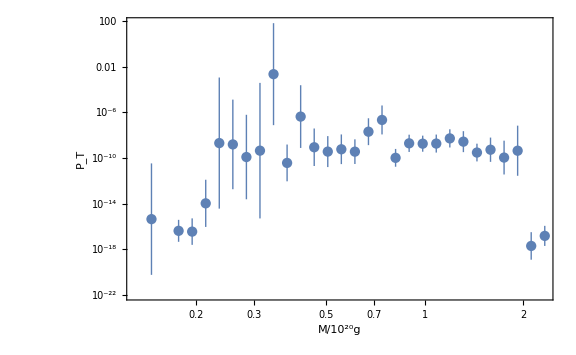

```mathematica
ListLogLogPlot[MassPBHList,PlotRange->All(*{{0.3,2.5},{10^-21,10^-1}}*),Joined->False,FrameLabel->{"M/10^20g","P_T"},GridLines->{{},{10^-9}}]
```

```mathematica
fPBHList=Table[{MassPBHList[[nn,1]],MassPBHList[[nn,1]]/(6.62 10^-13)MassPBHList[[nn,2]]},{nn,1,Length[MassPBHList]}];
```

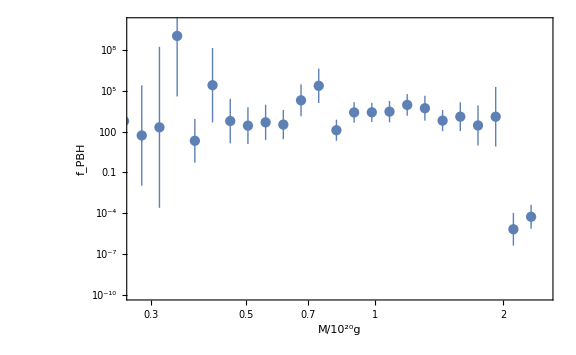

```mathematica
ListLogLogPlot[fPBHList,PlotRange->{{0.275,2.5},{10^-10,10^10}},Joined->False,FrameLabel->{"M/10^20g","f_PBH"},GridLines->{{},{10^4}}]
```

```mathematica
WCbar=Table[{10^-20 Mass[CintPBH[[i]],LatticeSize RmaxPBH[[i]]],Log10[Exp[logwPBH[[i]]]]},{i,1,PBHlength}];
```

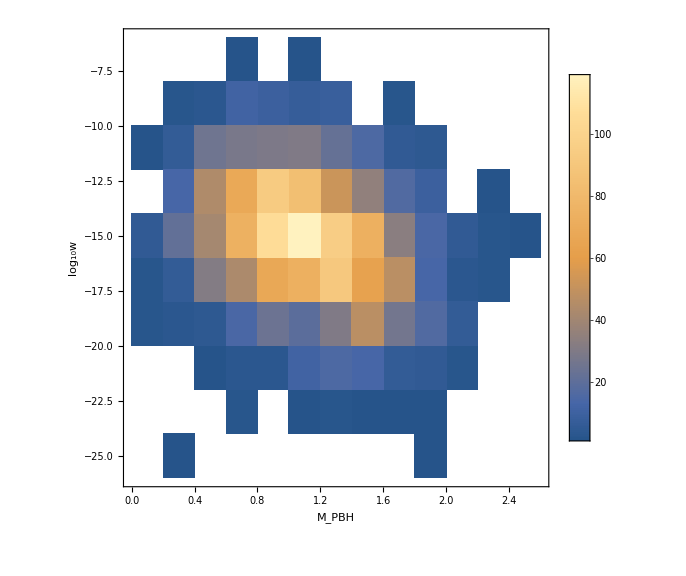

```mathematica
DensityHistogram[WCbar,12,FrameLabel->{"M_PBH","log_10w"},ChartLegends->Automatic,AspectRatio->1]
```

## Odeint test

### Chaotic

```mathematica
para={m->2111 10^-5};
```

```mathematica
V[x_]:=1/2 m^2 x^2/.para
```

```mathematica
H[x_,p_]:=√(1/3(p^2/2+V[x]))
```

```mathematica
ϵH[x_,p_]:=p^2/(2 H[x,p]^2);
```

```mathematica
t0=0;ϕi=11;dϕi=-0 √(2/3)m/.para;Hi=H[ϕi,dϕi];
```

```mathematica
tf=200 Hi^-1;tf//N
```

2109.72

```mathematica
sol=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+V'[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]]/.para,ϕ[t0]==ϕi,dϕ[t0]==dϕi,NN[t0]==0},{ϕ[t],dϕ[t],NN[t]},{t,t0,tf},MaxSteps->Infinity][[1]];
```

```mathematica
Φsol[t_]=ϕ[t]/.sol;
dΦsol[t_]=dϕ[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=H[Φsol[t],dΦsol[t]];
ϵHsol[t_]=ϵH[Φsol[t],dΦsol[t]];
```

```mathematica
Fig=ParametricPlot[{Nsol[t],Φsol[t]},{t,t0,tf},PlotStyle->{(*Dotted,*)Black}];
dϕFig=ParametricPlot[{Nsol[t],dΦsol[t]},{t,t0,tf},PlotStyle->{Dotted,Black}];
HFig=ParametricPlot[{Nsol[t],Hsol[t]},{t,t0,tf},PlotStyle->{Dotted,Black}];
```

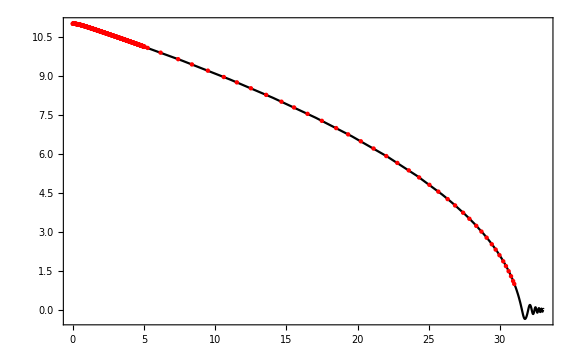

```mathematica
Osciadta=Import["Hybrid/Langevin.dat"];
x0data=Table[{Osciadta[[ii,1]],Osciadta[[ii,2]]},{ii,1,Length[Osciadta]}];
x1data=Table[{Osciadta[[ii,1]],Osciadta[[ii,3]]},{ii,1,Length[Osciadta]}];
Hdata=Table[{Osciadta[[ii,1]],Osciadta[[ii,4]]},{ii,1,Length[Osciadta]}];
Show[Fig,ListPlot[{x0data},Joined->False,PlotStyle->Red],PlotRange->All]
```

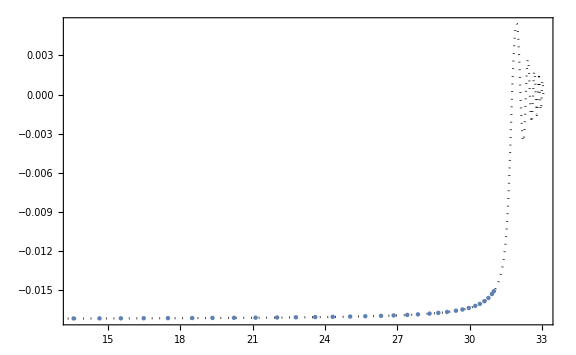

```mathematica
Show[dϕFig,ListPlot[{x1data},Joined->False]]
```

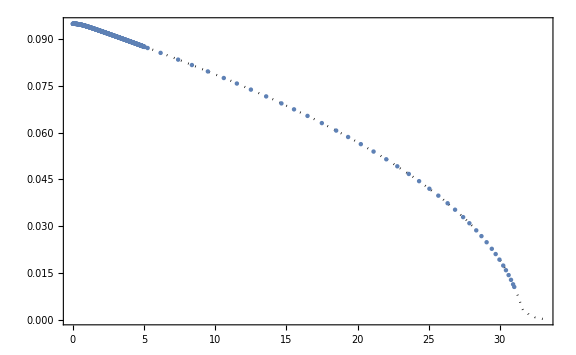

```mathematica
Show[HFig,ListPlot[Hdata,Joined->False],PlotRange->All]
```

```mathematica
ϵHFig=ParametricPlot[{Nsol[t],ϵHsol[t]},{t,t0,tf},PlotStyle->{Dotted,Black}];
```

```mathematica
ϵHdata=Table[{Osciadta[[ii,1]],ϵH[Osciadta[[ii,2]],Osciadta[[ii,3]]]},{ii,1,Length[Osciadta]}];
```

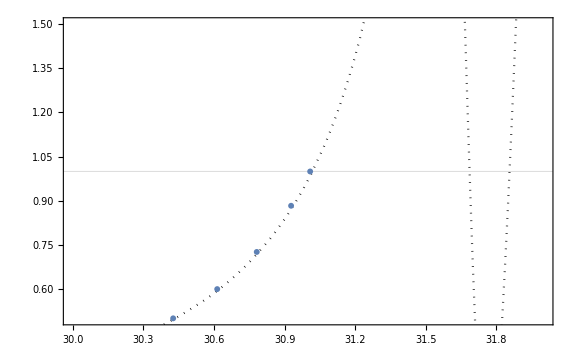

```mathematica
Show[ϵHFig,ListPlot[ϵHdata,Joined->False],GridLines->{None,{1}},PlotRange->{{30,32},{0.5,1.5}}]
```

## NoiseMap

### Map

```mathematica
NoiseMapData=Import["DFT/fft_NoiseMap.dat"];
num=Length[NoiseMapData[[1]]]^(1/3);
deltaN=Table[Table[Table[NoiseMapData[[1,num^2 (nz-1)+num(ny-1)+nx]],{nx,num}],{ny,num}],{nz,num}];
ListDensityPlot3D[deltaN,BoxRatios->{1, 1, 1},ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics3D-

### Power Spectrum

```mathematica
num=Length[NoiseMapData[[1]]]^(1/3)
```

64

```mathematica
deltaN=Table[Table[Table[NoiseMapData[[1,num^2 (nz-1)+num(ny-1)+nx]],{nx,num}],{ny,num}],{nz,num}];
```

```mathematica
ListDensityPlot3D[deltaN,BoxRatios->{1, 1, 1},ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(** Fourier transformation 1<kx<num **)
```

```mathematica
ζk[kx_,ky_,kz_]=1/num^(3/2)Sum[deltaN[[xz,xy,xx]] ⅇ^(-(2π ⅈ)/num((xx-1)(kx-1)+(xy-1)(ky-1)+(xz-1)(kz-1))),{xx,num},{xy,num},{xz,num}];
```

```mathematica
(** Count Subscript[N, k] **)
```

```mathematica
norm3[x_,y_,z_]=√((x-1)^2+(y-1)^2+(z-1)^2);
```

```mathematica
normdat=Table[Table[Table[norm3[nx,ny,nz],{nx,num}],{ny,num}],{nz,num}]//Simplify;
```

```mathematica
ck=0.01;
```

```mathematica
lnk[ll_]=(1+ck)^(ll-1)-1;
```

```mathematica
klist={};lk=0;
```

```mathematica
Do[If[lnk[ii]<√3(num-1),klist=Join[klist,{lnk[ii]}];lk++;,Break;],{ii,1,1000}]
klist=Join[klist,{lnk[lk+1]}];
ksize=klist//Length;
```

```mathematica
Nklist=Table[Length[Select[Select[Flatten[Flatten[normdat]],#≥lnk[nk]&],#<lnk[nk+1]&]],{nk,ksize}];
```

```mathematica
Nk=0;ζtemp=0;
```

```mathematica
ζeList[ii_]:=Select[Flatten[Table[If[klist[[ii]]<=norm3[nx,ny,nz]<klist[[ii+1]],Abs[ζk[nx,ny,nz]]^2,None],{nz,num},{ny,num},{nx,num}],2],Positive]
```

```mathematica
ζe=ParallelTable[ζeList[ii],{ii,ksize-1}];//AbsoluteTiming
ζt=Table[Total[ζe[[ii]]],{ii,Length[ζe]}];
```

{52.1062,Null}

```mathematica
tab=Table[Around[Sum[ζe[[jj,ll]],{ll,Length[ζe[[jj]]]}],If[Length[ζe[[jj]]]>1,Sqrt[Nklist[[jj]]]StandardDeviation[ζe[[jj]]],0]],{jj,Length[ζe]}];
```

```mathematica
taberr=Table[{klist[[ii]],tab[[ii]]/(num^3 ck)},{ii,Length[tab]}];
```

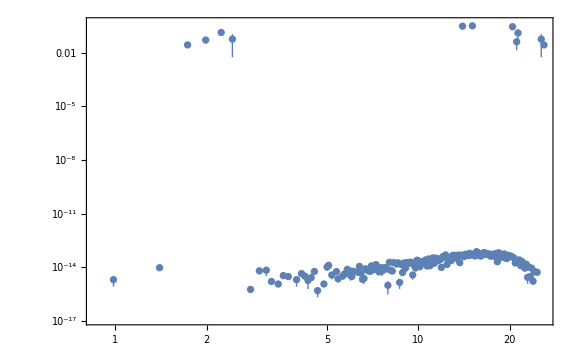

```mathematica
ListLogLogPlot[taberr,PlotRange->All(*{10^-5,10^2}*),Frame->True,Joined->False]
```

```mathematica
(** Check the variance **)
```

```mathematica
flatdN=deltaN//Flatten;
```

```mathematica
(*num^-3(flatdN.flatdN)*)
Variance[flatdN]
```

0.110392

```mathematica
ck Total[ζt]/(num^3 ck)
```

0.110365

```mathematica
Simplify[FourierTransform[1/(√((2π) σ^2))ⅇ^((-(kx-μ)^2)/σ^2),{kx,ky,kz},{x,y,z}],σ>0]
```

ⅇ^(-1/4 x (-4 ⅈ μ+x σ^2)) √π DiracDelta[y] DiracDelta[z]

### Animation

```mathematica
LatticeMapData=Import["DFT/fft_NoiseMap.dat"];
```

```mathematica
num=Length[First[LatticeMapData]]^(1/3)
```

32

```mathematica
zetaList=Table[LatticeMapData[[efoldN,num^2 (nz-1)+num(ny-1)+nx]],{efoldN,Length[LatticeMapData]},{nx,num},{ny,num},{nz,num}];
```

```mathematica
Dzeta=4(*3Sqrt[Variance[Last[zetaList]//Flatten]]*);
```

```mathematica
zetaPlotList=Table[ListDensityPlot3D[zetaList[[i]],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(i-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large],{i,2,Length[zetaList]}];
```

```mathematica
Export["zetamap.gif",zetaPlotList];//AbsoluteTiming
Beep[]
```

{40.4165,Null}

```mathematica
zetaPlotList[[40]]
```

-Graphics3D-

```mathematica
Last[zetaPlotList]
```

-Graphics3D-

## Lattice (chaotic_biased)

```mathematica
V[x_]=1/2 m^2 x^2;
ϵV[x_]=1/2(V'[x]/V[x])^2;
```

```mathematica
1/(24 π^2)V[x]/ϵV[x]/.{x->15,m->10^-5}//N
```

5.34311×10^-9

```mathematica
Solve[1/(24 π^2)V[x]/ϵV[x]==10^-2,m][[2]]/.{x->15}//N
```

{m→0.0136805}

### Annimation

```mathematica
LatticeMapData=Import["Lattice_chaotic_biased_g.dat"];
```

```mathematica
num=Length[First[LatticeMapData]]^(1/3)
```

17

```mathematica
ksigma[NN_]=(2π σ E^NN)/num/.{σ->10^-1};
```

```mathematica
(2π)/ksigma[3]//N
```

8.4638

```mathematica
zetaList=Table[LatticeMapData[[efoldN,num^2 (nz-1)+num(ny-1)+nx]],{efoldN,Length[LatticeMapData]},{nx,num},{ny,num},{nz,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[Last[zetaList]//Flatten]]
```

11.1204

```mathematica
zetaPlotList=Table[ListDensityPlot3D[zetaList[[i]],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(i-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large],{i,2,Length[zetaList]}];
```

```mathematica
Export["zetamap_chaotic_biased.gif",zetaPlotList];//AbsoluteTiming
```

{14.4929,Null}

```mathematica
Last[zetaPlotList]
```

-Graphics3D-

### Power Spectrum

```mathematica
NclMap=Map[#[[2]]&,Sort[Import["Ncl_chaotic_biased_g.dat"]]];
```

```mathematica
num=Length[NclMap]^(1/3)
```

17

```mathematica
NclMean=Mean[NclMap]
```

57.3894

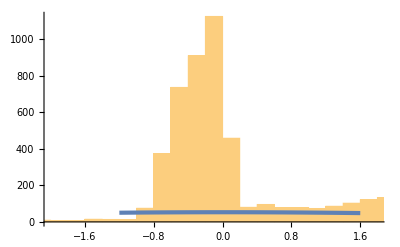

```mathematica
Show[Histogram[NclMap-NclMean],Plot[(num^3 0.1)/Sqrt[2π σ2] Exp[-x^2/(2σ2)]/.{σ2->Variance[NclMap]},{x,-1.2,1.6}]]
```

```mathematica
zeta=Table[NclMap[[num^2 (nz-1)+num(ny-1)+nx]]-NclMean,{nz,num},{ny,num},{nx,num}];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta//Flatten]]
```

11.1254

```mathematica
dNFig=ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->δ N==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["zetamap_chaotic_biased.pdf",dNFig];
```

```mathematica
dr=1;
Clear[zetardata]
zetardata[r_]:=Select[Flatten[Table[If[(r-dr/2)^2<=(i-1)^2+(j-1)^2+(k-1)^2<(r+dr/2)^2,zeta[[i,j,k]],None],{i,num},{j,num},{k,num}],2],NumberQ]
```

```mathematica
zetarList=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>1,{r,Mean[zetardatas]±StandardDeviation[zetardatas]/Sqrt[Length[zetardatas]]},None],{r,1,num Sqrt[3]}],Length[#]>1&];
zetarListwoError=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>1,{r,Mean[zetardatas]},None],{r,1,num Sqrt[3]}],Length[#]>1&];
```

```mathematica
ksigma[NN_]=(2π σ E^NN)/num/.{σ->10^-1};
```

```mathematica
fit=FindFit[zetarListwoError,A Sin[ksigma[3]r]/(ksigma[3]r),A,r]
```

{A→60.0845}

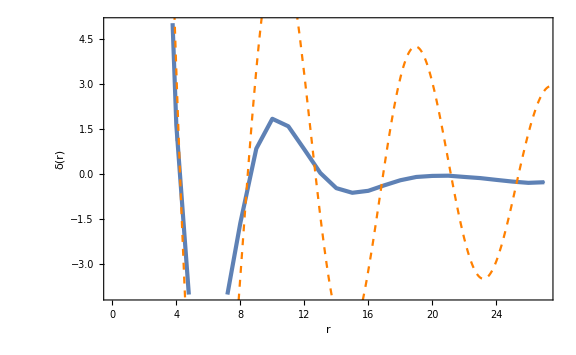

```mathematica
Show[ListPlot[zetarList,FrameLabel->{r,"δ(r)"},PlotLegends->Placed[LineLegend[{"lattice"},LegendMarkerSize->30],{0.8,0.8}]],Plot[A Sin[ksigma[3]r]/(ksigma[3]r)/.fit,{r,0,num Sqrt[3]},PlotStyle->{Orange,Dashed},PlotLegends->Placed[LineLegend[{"(sin (SubscriptBox[k, σ] r))/k_σ"},LegendMarkerSize->30],{0.8,0.8}]]]
```

```mathematica
ListDensityPlot3D[zeta,BoxRatios->{1, 1, 1},ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,Ticks->None,ImageSize->Large,ViewPoint->Left,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
(** Fourier transformation 1<kx<num **)
```

```mathematica
ζk[kx_,ky_,kz_]=1/num^(3/2)Sum[zeta[[xz,xy,xx]] ⅇ^(-(2π ⅈ)/num((xx-1)(kx-1)+(xy-1)(ky-1)+(xz-1)(kz-1))),{xx,num},{xy,num},{xz,num}];
```

```mathematica
(** Count Subscript[N, k] **)
```

```mathematica
norm3[x_,y_,z_]=√((x-1)^2+(y-1)^2+(z-1)^2);
```

```mathematica
normdat=Table[Table[Table[norm3[nx,ny,nz],{nx,num}],{ny,num}],{nz,num}]//Simplify;
```

```mathematica
ck=0.01;
```

```mathematica
lnk[ll_]=(1+ck)^(ll-1)-1;
```

```mathematica
klist={};lk=0;
```

```mathematica
Do[If[lnk[ii]<√3(num-1),klist=Join[klist,{lnk[ii]}];lk++;,Break;],{ii,1,1000}]
klist=Join[klist,{lnk[lk+1]}];
ksize=klist//Length;
```

```mathematica
Nklist=Table[Length[Select[Select[Flatten[Flatten[normdat]],#≥lnk[nk]&],#<lnk[nk+1]&]],{nk,ksize}];
```

```mathematica
Nk=0;ζtemp=0;
```

```mathematica
ζeList[ii_]:=Select[Flatten[Table[If[klist[[ii]]<=norm3[nx,ny,nz]<klist[[ii+1]],Abs[ζk[nx,ny,nz]]^2,None],{nz,num},{ny,num},{nx,num}],2],Positive]
```

```mathematica
ζe=Table[ζeList[ii],{ii,ksize-1}];//AbsoluteTiming
ζt=Table[Total[ζe[[ii]]],{ii,Length[ζe]}];
```

{91.6158,Null}

```mathematica
tab=Table[Around[Sum[ζe[[jj,ll]],{ll,Length[ζe[[jj]]]}],If[Length[ζe[[jj]]]>1,Sqrt[Nklist[[jj]]]StandardDeviation[ζe[[jj]]],0]],{jj,Length[ζe]}];
```

```mathematica
taberr=Table[{klist[[ii]],tab[[ii]]/(num^3 ck)},{ii,Length[tab]}];
```

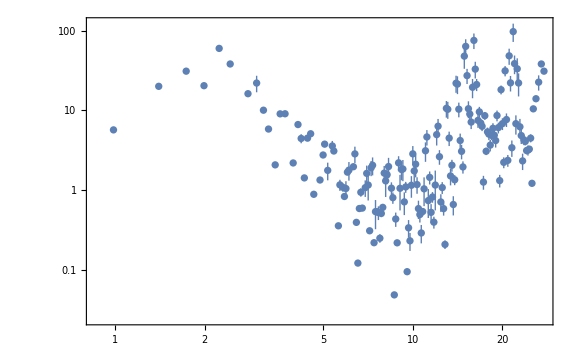

```mathematica
ListLogLogPlot[taberr(*,PlotRange->{10^-10,1.5 10^-7}*),Frame->True,Joined->False]
```

```mathematica
(** Check the variance **)
```

```mathematica
flatζ=zeta//Flatten;
```

```mathematica
(*num^-3(flatdN.flatdN)*)
Variance[flatζ]
```

13.7527

```mathematica
ck Total[ζt]/(num^3 ck)
```

13.7499

## Perturbation

### Chaotic

```mathematica
para={m->33 10^-3};
```

```mathematica
V[x_]:=1/2 m^2 x^2/.para
```

```mathematica
H[x_,p_]:=√(1/3(p^2/2+V[x]))
```

```mathematica
ϵH[x_,p_]:=p^2/(2 H[x,p]^2);
```

```mathematica
t0=0;ϕi=15;dϕi=-√(2/3)m/.para;Hi=H[ϕi,dϕi];
```

```mathematica
tf=200 Hi^-1;tf//N
```

988.23

```mathematica
sol=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+V'[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[t0]==ϕi,dϕ[t0]==dϕi,NN[t0]==0},{ϕ[t],dϕ[t],NN[t]},{t,t0,tf},MaxSteps->Infinity][[1]];
```

```mathematica
Φsol[t_]=ϕ[t]/.sol;
dΦsol[t_]=dϕ[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=H[Φsol[t],dΦsol[t]];
ϵHsol[t_]=ϵH[Φsol[t],dΦsol[t]];
```

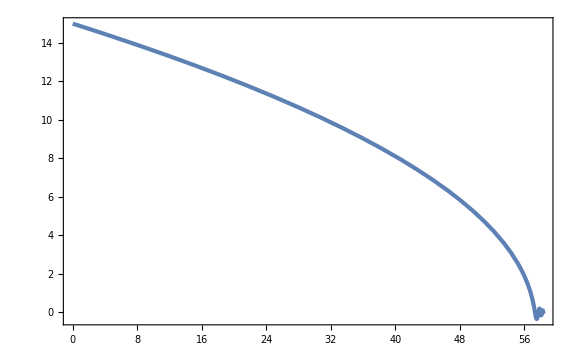

```mathematica
ParametricPlot[{Nsol[t],Φsol[t]},{t,t0,tf},PlotRange->All,AspectRatio->1/GoldenRatio,GridLines->{None,{√2}}]
```

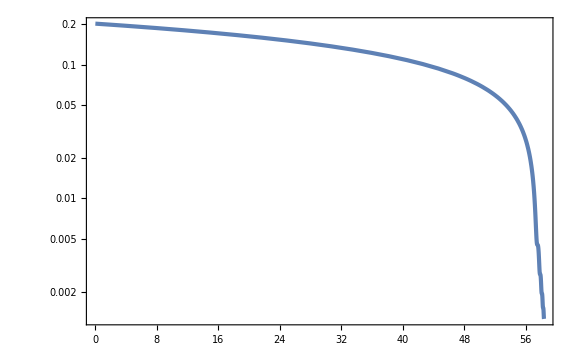

```mathematica
ParametricPlot[{Nsol[t],Hsol[t]},{t,t0,tf},PlotRange->All,ScalingFunctions->{Identity,"Log"}]
```

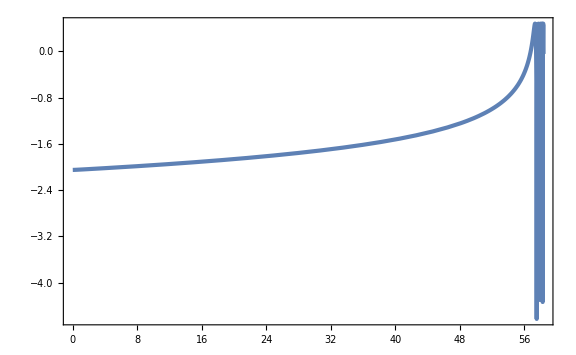

```mathematica
ParametricPlot[{Nsol[t],Log10[ϵHsol[t]]},{t,t0,tf},PlotRange->All]
```

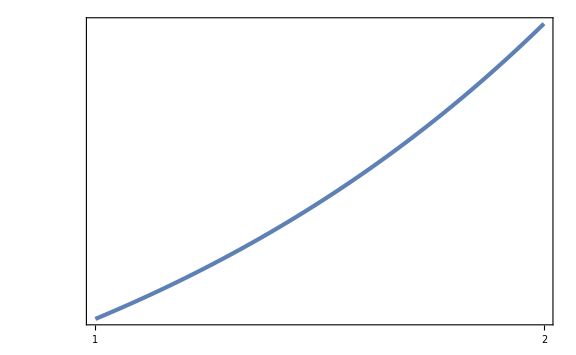

```mathematica
LogLogPlot[ϵHsol[t],{t,1,2},PlotRange->All,GridLines->{None,{1}}]
```

```mathematica
tend=t/.FindRoot[{ϵHsol[t]==1},{t,9 10^2,0,1.9 10^3}]
Nend=Nsol[tend]
```

891.631

58.2428

```mathematica
tsqrt2=t/.FindRoot[Φsol[t]==√2,{t,6 10^2}]
Nsqrt2=Nsol[tsqrt2]
```

510.455

56.4693

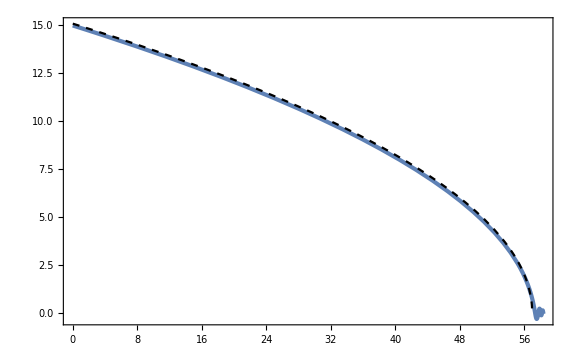

```mathematica
(** 解析解との比較 **)
Show[ParametricPlot[{Nsol[t],Φsol[t]},{t,0,tf},PlotRange->All,AspectRatio->1/GoldenRatio],Plot[Sqrt[4(Nsqrt2-NN)+2],{NN,0,Nend},PlotStyle->{Dashed,Black}]]
```

```mathematica
(** classical δN **)
```

```mathematica
tempt=20 Hi^-1;
```

```mathematica
solp=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+V'[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[tempt]==Φsol[tempt]+Hsol[tempt]/(2π),dϕ[tempt]==dΦsol[tempt],NN[tempt]==Nsol[tempt]},{ϕ[t],dϕ[t],NN[t]},{t,tempt,tf},MaxSteps->Infinity][[1]];
```

```mathematica
Φsolp[t_]=ϕ[t]/.solp;
Nsolp[t_]=NN[t]/.solp;
```

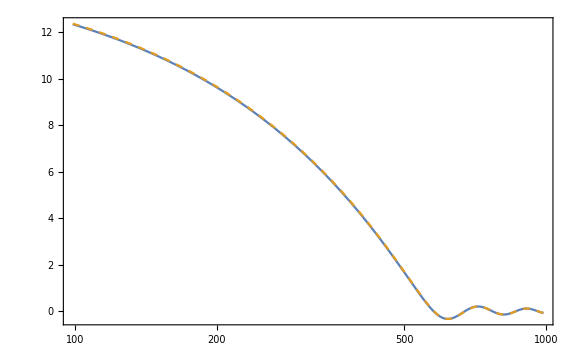

```mathematica
LogLinearPlot[{Φsol[t],Φsolp[t]},{t,tempt,tf},PlotRange->All,PlotStyle->{{},{Dashed}}]
```

```mathematica
Nsqrt2p=Nsolp[t]/.FindRoot[Φsolp[t]==√2,{t,10^2}]
```

56.6338

```mathematica
Nsqrt2p-Nsqrt2
```

0.164546

```mathematica
Nsol[tempt]
```

18.2332

```mathematica
{Nsol[tempt],(Nsqrt2p-Nsqrt2)^2}
```

{18.2332,0.0270754}

```mathematica
(** temptを動かすことでリストを作る **)
```

```mathematica
(*Table[{Nsol[tt],(Nsqrt2-Nsqrt2p)},{tt,10}]*)
```

```mathematica
Nmax=61;
```

```mathematica
tlist=Table[nn Hi^-1,{nn,1,Nmax}];
```

```mathematica
tlist=Table[nn ,{nn,1,tsqrt2,Hi^-1}];
```

```mathematica
dNMod[k_]:=Module[{tmpt},tmpt=tlist[[k]];soltemp=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+V'[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[tmpt]==Φsol[tmpt]+Hsol[tmpt]/(2π),dϕ[tmpt]==dΦsol[tmpt],NN[tmpt]==Nsol[tmpt]},{ϕ[t],dϕ[t],NN[t]},{t,tmpt,tf},MaxSteps->Infinity][[1]];
Φsolt[k,t_]=ϕ[t]/.soltemp;
Nsolt[k,t_]=NN[t]/.soltemp;Nsqrt2temp=Nsolt[k,t]/.FindRoot[Φsolt[k,t]==√2,{t,tmpt}];(Nsqrt2temp-Nsqrt2)^2]
```

```mathematica
dNmap=Table[{Nsol[tlist[[tt]]],dNMod[tt]},{tt,1,Length[tlist]}];
```

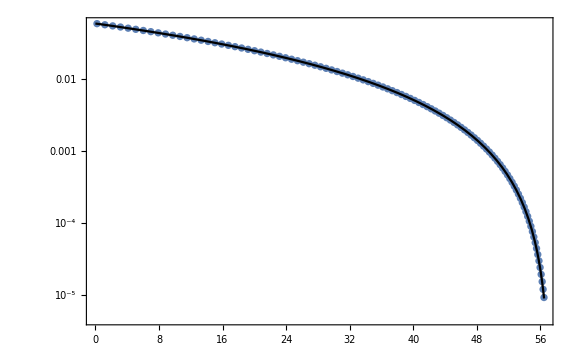

```mathematica
Show[ListLogPlot[dNmap,Joined->False],ParametricPlot[{Nsol[t],1/(2ϵHsol[t])(Hsol[t]/(2π))^2},{t,0,tsqrt2},PlotRange->All,ScalingFunctions->{Identity,"Log"},PlotStyle->Black]]
```

```mathematica
(** GOOD **)
```

```mathematica
calPzlist=Table[soltemp=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+V'[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[tmpt]==Φsol[tmpt]+Hsol[tmpt]/(2π),dϕ[tmpt]==dΦsol[tmpt],NN[tmpt]==Nsol[tmpt]},{ϕ[t],dϕ[t],NN[t]},{t,tmpt,tf},MaxSteps->Infinity][[1]];
Φsolt[k,t_]=ϕ[t]/.soltemp;
Nsolt[k,t_]=NN[t]/.soltemp;Nsqrt2temp=Nsolt[k,t]/.FindRoot[Φsolt[k,t]==√2,{t,tmpt}];{Nsol[tmpt],(Nsqrt2temp-Nsqrt2)^2},{tmpt,1,tsqrt2,Hi^-1}];
```

```mathematica
Show[ListLogPlot[calPzlist,Joined->False],ParametricPlot[{Nsol[t],1/(2ϵHsol[t])(Hsol[t]/(2π))^2},{t,0,tsqrt2},PlotRange->All,ScalingFunctions->{Identity,"Log"},PlotStyle->Black]]
```

-Graphics-

```mathematica
(** powerから計算 **)
```

```mathematica
vc[k_,τ_]:=√(π/(4k))√(-k τ)HankelH1[3/2,-k τ]
```

```mathematica
δϕc[k_,t_]=(√π)/2 Hsol[t](-1/(Exp[Nsol[t]]Hsol[t]))^(3/2)HankelH1[3/2(*-m^2/(3 Hsol[t]^2)*),-k -1/(Exp[Nsol[t]]Hsol[t])](*1/(a0 Exp[Nsol[t]-N0])vc[k,-1/(a0 Exp[Nsol[t]-N0]Hsol[t])]*);
```

```mathematica
calPσ[t_]:=k^3/(2 π^2)Abs[δϕc[k,t]]^2/.{k->σ a0 Exp[Nsol[t]-N0]Hsol[t]}/.para
```

```mathematica
σ=10^-2;a0=1(*Hsol[t0]^-1*);N0=0;
```

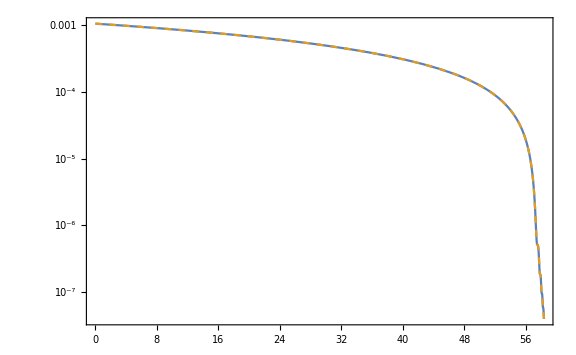

```mathematica
ParametricPlot[{{Nsol[t],calPσ[t]},{Nsol[t],(Hsol[t]/(2π))^2}},{t,0,tf},PlotRange->All,PlotStyle->{{},{Dashed}},ScalingFunctions->{Identity,"Log"}]
```

```mathematica
calPzlist=Table[soltemp=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+V'[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[tmpt]==Φsol[tmpt]+√calPσ[tmpt],dϕ[tmpt]==dΦsol[tmpt],NN[tmpt]==Nsol[tmpt]},{ϕ[t],dϕ[t],NN[t]},{t,tmpt,tf},MaxSteps->Infinity][[1]];
Φsolt[k,t_]=ϕ[t]/.soltemp;
Nsolt[k,t_]=NN[t]/.soltemp;Nsqrt2temp=Nsolt[k,t]/.FindRoot[Φsolt[k,t]==√2,{t,tmpt}];{Nsol[tmpt],(Nsqrt2temp-Nsqrt2)^2},{tmpt,1,tsqrt2,Hi^-1}];
```

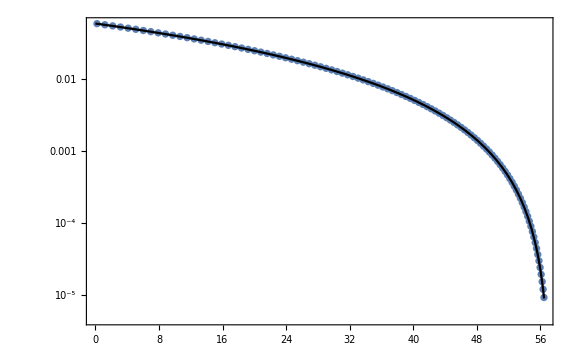

```mathematica
Show[ListLogPlot[calPzlist,Joined->False],ParametricPlot[{Nsol[t],1/(2ϵHsol[t])(Hsol[t]/(2π))^2},{t,0,tsqrt2},PlotRange->All,ScalingFunctions->{Identity,"Log"},PlotStyle->Black]]
```

### Broken Liner

#### Perturbation

```mathematica
para={𝒫IR->85 10^-11,Λ->17 10^2,H0->10^-5};
```

```mathematica
τ0=-1;
```

```mathematica
Ap=√((9 H0^6)/(4 π^2 𝒫IR))/.para;Am=Ap/Λ/.para;a0=-1/(τ0 H0);
```

```mathematica
(*Subscript[ℋ, 0]=Subscript[a, 0] Subscript[H, 0]=1, κ=-Subscript[kτ, 0]=k*)
```

```mathematica
C1[k_]:=-1/2 √(π/k)
```

```mathematica
D1[k_]:=0
```

```mathematica
C2[k_]:=-1/2 √(π/k)+I 1/2 √(π/k)3/2(1-1/Λ)(1/k^3+1/k)/.para
```

```mathematica
D2[k_]:=-1/2 √(π/k)3/2(1-1/Λ)((1/k^3-1/k)Sin[2k]-2/k^2 Cos[2k])+I 1/2 √(π/k)3/2(1-1/Λ)((1/k^3-1/k)Cos[2k]+2/k^2 Sin[2k])
```

```mathematica
v1[k_,τ_]:=C1[k] √(-k τ)HankelH1[3/2,-k τ]+D1[k] √(-k τ)HankelH2[3/2,-k τ]
vp1[k_,τ_]=D[v1[k,τ], τ]//Simplify;
v2[k_,τ_]:=C2[k] √(-k τ)HankelH1[3/2,-k τ]+D2[k] √(-k τ)HankelH2[3/2,-k τ]/.para
vp2[k_,τ_]=D[v2[k,τ], τ]/.para//Simplify;
```

```mathematica
vk[k_,τ_]:=v1[k,τ]/;τ<τ0
vk[k_,τ_]:=v2[k,τ]/;τ≥τ0
```

```mathematica
vkp[k_,τ_]:=vp1[k,τ]/;τ<τ0
vkp[k_,τ_]:=vp2[k,τ]/;τ≥τ0
```

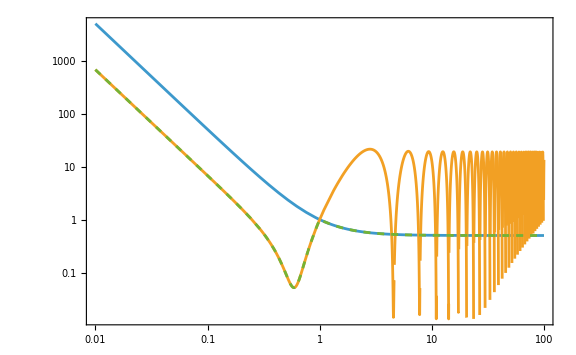

```mathematica
LogLogPlot[{Abs[v1[1,t]^2],Abs[v2[1,-t]^2],Abs[vk[1,-t]^2]/.para},{t,10^-2,10^2},PlotRange->All,PlotStyle->{{},{},{Dashed}}]
```

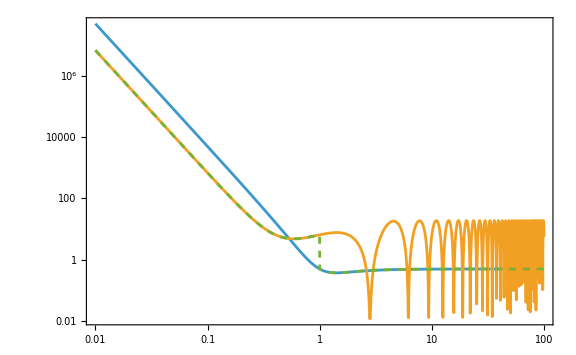

```mathematica
LogLogPlot[{Abs[vp1[1,-t]^2],Abs[vp2[1,-t]^2],Abs[vkp[1,-t]^2]/.para},{t,10^-2,10^2},PlotRange->All,PlotStyle->{{},{},{Dashed}}]
```

```mathematica
z2[τ_]:=-a0/(3 H0^2)(Am(τ/τ0)^-1+(Ap-Am)(τ/τ0)^2)
```

```mathematica
z[τ_]:=-a0/(3 H0^2)Ap(τ/τ0)^-1/;τ<τ0
z[τ_]:=-a0/(3 H0^2)(Am(τ/τ0)^-1+(Ap-Am)(τ/τ0)^2)/;τ≥τ0
```

```mathematica
calRk[k_,τ_]:=v1[k,τ]/z[τ]/;τ<τ0
calRk[k_,τ_]:=v2[k,τ]/z[τ]/;τ≥τ0
```

```mathematica
calPk[k_]=FullSimplify[k^3/(2 π^2)Series[v2[k,τ]/z2[τ],{τ,0,0}]Conjugate[Series[v2[k,τ]/z2[τ],{τ,0,0}]]/.para//Normal,{k>0}]
```

(17 (25979409+51958818 k^2+25979409 k^4+5780000 k^6+5097 ((-5097+11897 k^4) Cos[2 k]+2 k (-5097-6797 k^2+1700 k^4) Sin[2 k])))/(40000000000 k^6)

```mathematica
𝒫Rnum[κ_]:=𝒫IR((9(Λ-1)^2)/κ^6(Sin[κ]-κ Cos[κ])^4+(Λ+(3(Λ-1))/(2 κ^3)((κ^2-1)Sin[2κ]+2κ Cos[2κ]))^2)
```

```mathematica
𝒫Rnum[k]//TeXForm
```

\text{$\mathcal{P}$IR} \left(\frac{9 (\Lambda -1)^2 (\sin (k)-k \cos (k))^4}{k^6}+\left(\frac{3 (\Lambda -1) \left(\left(k^2-1\right) \sin (2 k)+2 k \cos (2 k)\right)}{2
   k^3}+\Lambda \right)^2\right)

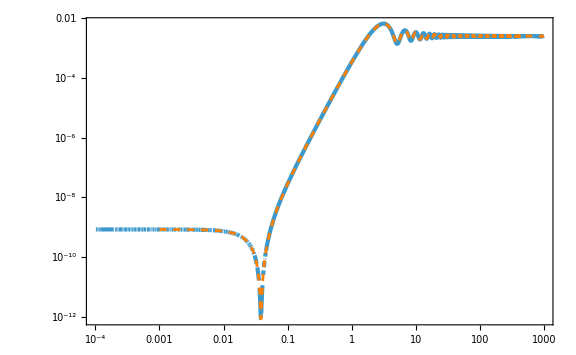

```mathematica
Show[LogLogPlot[calPk[k],{k,10^-4,10^3},PlotRange->All,WorkingPrecision->50],LogLogPlot[𝒫Rnum[k]/.para,{k,10^-3,10^3},PlotStyle->{Dashed,Orange}]]
```

#### Classical δN

```mathematica
Clear[H,V,Vp]
```

```mathematica
H[x_,p_]:=√(1/3(p^2/2+V[x]))
```

```mathematica
ϵH[x_,p_]:=p^2/(2 H[x,p]^2);
```

```mathematica
(*para={𝒫IR->85 10^-11,Λ->10^4,H0->10^-5};*)
```

```mathematica
(*τ0=-1;*)
```

```mathematica
(*Ap=√((9 H0^6)/(4 π^2 𝒫IR))/.para;Am=Ap/Λ/.para;a0=-1/(τ0 H0);*)
```

```mathematica
H0=10^-5;
```

```mathematica
V0=3 H0^2;
```

```mathematica
V[x_]:=V0+Ap x/;x>0
V[x_]:=V0+Am x/;x≤0
Vp[x_]:=Ap/;x>0
Vp[x_]:=Am /;x≤0
```

```mathematica
xi=516 10^-3;pi=-0;Hi=H[xi,pi];ti=0;tf=40 Hi^-1;
```

```mathematica
solb=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+Vp[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[ti]==xi,dϕ[ti]==pi,NN[ti]==0},{ϕ[t],dϕ[t],NN[t]},{t,ti,tf},MaxSteps->Infinity,WorkingPrecision->50][[1]];
```

```mathematica
Φsol[t_]=ϕ[t]/.solb;
dΦsol[t_]=dϕ[t]/.solb;
Nsol[t_]=NN[t]/.solb;
Hsol[t_]=H[Φsol[t],dΦsol[t]];
ϵHsol[t_]=ϵH[Φsol[t],dΦsol[t]];
```

```mathematica
sample=-18300 10^-6;
```

```mathematica
t0=t/.FindRoot[Φsol[t]==0,{t,Hi^-1},WorkingPrecision->50];t0 Hi;
N0=Nsol[t0]
```

9.927615610417597850317117551652351014032561934816

```mathematica
tend=t/.FindRoot[Φsol[t]==sample,{t,Hi^-1},WorkingPrecision->50];t0 Hi;
Nend=Nsol[tend]
```

13.95266743928072542555953758646293466475812391731

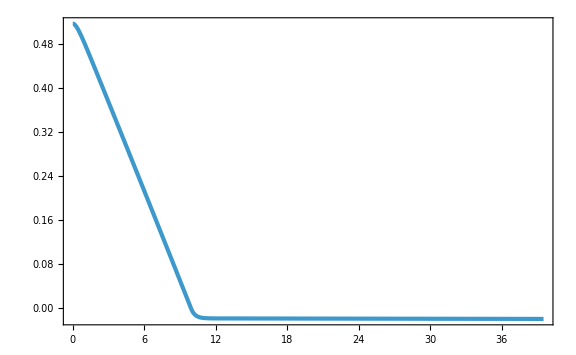

```mathematica
ParametricPlot[{Nsol[t],Φsol[t]},{t,ti(*+11 Hi^-1*),tf},PlotRange->All,PlotPoints->500,GridLines->{{N0},{sample}}]
```

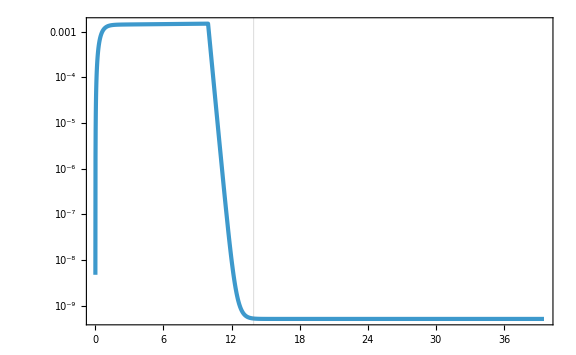

```mathematica
ParametricPlot[{Nsol[t],ϵHsol[t]},{t,ti,tf},ScalingFunctions->{Identity,"Log"},GridLines->{{Nend},None}]
```

```mathematica
(** rescaling of a0 **)
```

```mathematica
ai=-1/(τ0 Hsol[t0])
```

99975.212446313915401784132552310895067593981420778

```mathematica
σ=(*10^-3*)10^-1;
```

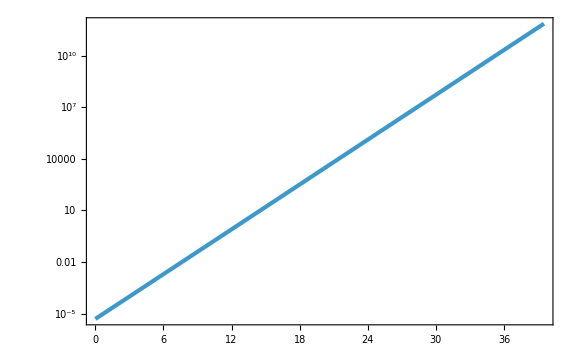

```mathematica
ParametricPlot[{Nsol[t],σ ai Hsol[t] Exp[Nsol[t]-N0]},{t,ti,tf},ScalingFunctions->{Identity,"Log"}]
```

ParametricPlot::precw: 引数関数({Divide[1.14920810465590035537448780926367560888601233169366 Power[10, -32] Power[E, <<1>>] (25979409 + <<3>> + 5097 <<1>>), <<1>>] - 0, <<4>>})の精度がWorkingPrecision (50.)より小さくなっています．

ParametricPlot::precw: 引数関数({True, True, True, <<1>>, Re[V[InterpolatingFunction[{{0, 3.9448263467027756813854790601667892919247909371263 <<1>>}}, <>][t]] + Divide[<<2>>]] <= 0})の精度がWorkingPrecision (50.)より小さくなっています．

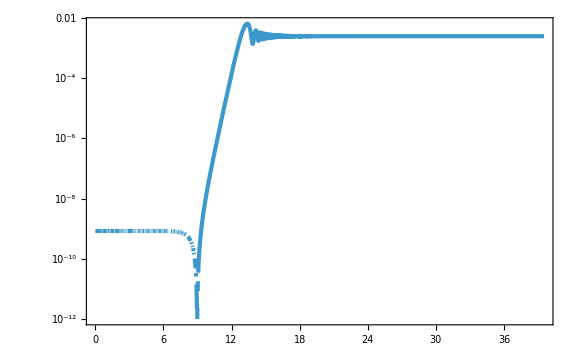

```mathematica
ParametricPlot[{Nsol[t],calPk[σ ai Hsol[t] Exp[Nsol[t]-N0]]},{t,ti,tf},PlotRange->All(*,PlotPoints->500*),ScalingFunctions->{Identity,"Log"},WorkingPrecision->50]
```

```mathematica
δϕ1[k_,t_]=1/(ai Exp[Nsol[t]-N0])v1[k,-1/(ai Exp[Nsol[t]-N0]Hsol[t])];
δϕ2[k_,t_]=1/(ai Exp[Nsol[t]-N0])v2[k,-1/(ai Exp[Nsol[t]-N0]Hsol[t])];
```

```mathematica
δϕk[k_,t_]:=δϕ1[k,t]/;t<t0
δϕk[k_,t_]:=δϕ2[k,t]/;t≥t0
```

```mathematica
calPσ[t_]:=k^3/(2 π^2)Abs[δϕk[k,t]]^2/.{k->σ ai Exp[Nsol[t]-N0]Hsol[t]}
```

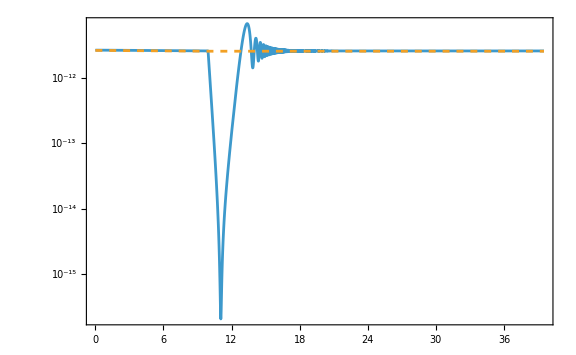

```mathematica
ParametricPlot[{{Nsol[t],calPσ[t]},{Nsol[t],(Hsol[t]/(2π))^2}},{t,ti,tf},ScalingFunctions->{Identity,"Log"},PlotRange->All,PlotStyle->{{},{Dashed}},PlotPoints->100]
```

```mathematica
tmpt=3 Hi^-1;
```

```mathematica
solbp=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+Vp[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[tmpt]==Φsol[tmpt]+√calPσ[tmpt],dϕ[tmpt]==dΦsol[tmpt],NN[tmpt]==Nsol[tmpt]},{ϕ[t],dϕ[t],NN[t]},{t,tmpt,tf},MaxSteps->Infinity,WorkingPrecision->50][[1]];
```

NDSolve::precw: 微分方程式({{√3 dϕ[t] √(Times[«2»]+V[«1»])+Vp[ϕ[t]]+dϕ'[t]==0,ϕ'[t]==dϕ[t],NN'[t]==(√(1/2 Power[«2»]+V[ϕ[«1»]]))/(√3),ϕ[3 √(3 Power[«2»])]==0.374232279171688444412720782822027813615069194465,dϕ[3 √(3 Power[«2»])]==-5.399528542428944109474149713970468053834730448611×10^-7,NN[3 √(3 Power[«2»])]==2.995490134345376594009575901047224945249327102209},{},{},{},{}})の精度がWorkingPrecision(50.)より小さくなっています．

```mathematica
Φsolp[t_]=ϕ[t]/.solbp;
dΦsolp[t_]=dϕ[t]/.solbp;
Nsolp[t_]=NN[t]/.solbp;
```

```mathematica
tendp=t/.FindRoot[Φsolp[t]==sample,{t,tmpt},WorkingPrecision->50];tendp Hi
Nendp=Nsolp[tendp]
```

14.073062171938990752126836340808089857931540463587

13.95269766349450723495787903288017022467859616774

```mathematica
{Nsol[tmpt],(Nendp-Nend)^2}
```

{2.995490134345376594009575901047224945249327102209,9.13503098728517172973381820243308354198222×10^-10}

```mathematica
(*ParametricPlot[{{Φsolp[t],dΦsolp[t]}(*,{Φsol[t],dΦsol[t]}*)},{t,tmpt,tf},PlotRange->All(*,PlotStyle->{{},{Dashed}}*),PlotPoints->500,GridLines->{{sample},None}]*)
```

```mathematica
calPzlist=Table[solbtmp=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+Vp[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[tmp]==Φsol[tmp]+√calPσ[tmp],dϕ[tmp]==dΦsol[tmp],NN[tmp]==Nsol[tmp]},{ϕ[t],dϕ[t],NN[t]},{t,tmp,tf},MaxSteps->Infinity,WorkingPrecision->50][[1]];
Φsolp[t_]=ϕ[t]/.solbtmp;
Nsolp[t_]=NN[t]/.solbtmp;
Nendp=Nsolp[t]/.FindRoot[Φsolp[t]==sample,{t,tmp},WorkingPrecision->50];
{Nsol[tmp],(Nendp-Nend)^2},{tmp,10^-1 Hi^-1,(*t0*)tend,((*t0*)tend-10^-1 Hi^-1)/100}];
```

NDSolve::precw: 微分方程式({{√3 dϕ[t] √(Times[«2»]+V[«1»])+Vp[ϕ[t]]+dϕ'[t]==0,ϕ'[t]==dϕ[t],NN'[t]==(√(1/2 Power[«2»]+V[ϕ[«1»]]))/(√3),ϕ[1/10 √(3 Power[«2»])]==0.5152792192357141959802830705421261645186245391526,dϕ[1/10 √(3 Power[«2»])]==-1.39534989487169934780310627224234605438108161004×10^-7,NN[1/10 √(3 Power[«2»])]==0.09999991128530234446776416270610473517804288023189},{},{},{},{}})の精度がWorkingPrecision(50.)より小さくなっています．

NDSolve::precw: 微分方程式({{√3 dϕ[t] √(Times[«2»]+V[«1»])+Vp[ϕ[t]]+dϕ'[t]==0,ϕ'[t]==dϕ[t],NN'[t]==(√(1/2 Power[«2»]+V[ϕ[«1»]]))/(√3),ϕ[23642.361903753436117872790656147438086380597248424]==«98»,dϕ[23642.361903753436117872790656147438086380597248424]==-2.761050540397630169903984564269593335331572694284×10^-7,NN[23642.361903753436117872790656147438086380597248424]==0.2397279901056036185420223370525529287293421765883},{},{},{},{}})の精度がWorkingPrecision(50.)より小さくなっています．

NDSolve::precw: 微分方程式({{√3 dϕ[t] √(Times[«2»]+V[«1»])+Vp[ϕ[t]]+dϕ'[t]==0,ϕ'[t]==dϕ[t],NN'[t]==(√(1/2 Power[«2»]+V[ϕ[«1»]]))/(√3),ϕ[37422.657940749933032281883661877902942949217154033]==«98»,dϕ[37422.657940749933032281883661877902942949217154033]==-3.65917272452762260817326318951302623088746677517×10^-7,NN[37422.657940749933032281883661877902942949217154033]==0.3794488339245015390326413496685402596629116170719},{},{},{},{}})の精度がWorkingPrecision(50.)より小さくなっています．

General::stop: この計算中に，NDSolve::precwのこれ以上の出力は表示されません．

$Aborted

ParametricPlot::precw: 引数関数({Divide[1.14920810465590035537448780926367560888601233169366 Power[10, -32] <<2>>, Power[V[Inte<<15>>on[<<2>>][t]] + Divide[<<2>>], 3]] - 0, <<4>>})の精度がWorkingPrecision (50.)より小さくなっています．

ParametricPlot::precw: 引数関数({True, True, True, <<1>>, Re[V[InterpolatingFunction[{{0, 3.9448263467027756813854790601667892919247909371263 Power[<<2>>]}}, <>][t]] + Divide[<<2>>]] <= 0})の精度がWorkingPrecision (50.)より小さくなっています．

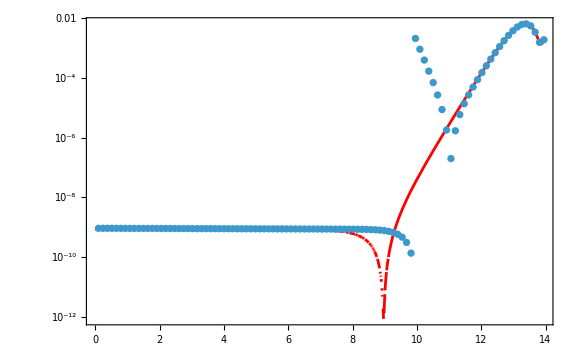

```mathematica
Show[ParametricPlot[{Nsol[t],calPk[σ ai Hsol[t] Exp[Nsol[t]-N0]]},{t,ti,tend},PlotRange->All,ScalingFunctions->{Identity,"Log"},PlotStyle->Red,WorkingPrecision->50],ListLogPlot[calPzlist,Joined->False,PlotRange->All]]
```

```mathematica
(*calPzlist=Table[soltemp=NDSolve[{dϕ'[t]+3H[ϕ[t],dϕ[t]]dϕ[t]+V'[ϕ[t]]==0,ϕ'[t]==dϕ[t],NN'[t]==H[ϕ[t],dϕ[t]],ϕ[tmpt]==Φsol[tmpt]+Hsol[tmpt]/(2π)(*√calPσ[tmpt]*),dϕ[tmpt]==dΦsol[tmpt],NN[tmpt]==Nsol[tmpt]},{ϕ[t],dϕ[t],NN[t]},{t,tmpt,tf},MaxSteps->Infinity][[1]];
Φsolt[k,t_]=ϕ[t]/.soltemp;
Nsolt[k,t_]=NN[t]/.soltemp;Nsqrt2temp=Nsolt[k,t]/.FindRoot[Φsolt[k,t]==10^-3,{t,tmpt}];{Nsol[tmpt],(Nsqrt2temp-N0)^2},{tmpt,ti+Hi^-1,t0,10^-1 Hi^-1}];*)
```

```mathematica
(*Show[ListLogPlot[calPzlist,Joined->False,PlotRange->All],ParametricPlot[{Nsol[t],calPk[σ a0 Hsol[t] Exp[Nsol[t]-N0]]},{t,ti,tf},PlotRange->All,ScalingFunctions->{Identity,"Log"},PlotStyle->Red]]*)
```

## Lattice (chaotic)

### Animation

```mathematica
AbsoluteTiming[HMapData=Import["STOLAS_single/data/chaotic/animation/H_64_0_0.dat"];
piMapData=Import["STOLAS_single/data/chaotic/animation/pi_64_0_0.dat"];]
```

{6.9971,Null}

```mathematica
num=Length[First[HMapData]]^(1/3)
```

16 2^(2/3)

```mathematica
HMeanList=Table[Mean[HMapData[[efoldN]]],{efoldN,Length[HMapData]}];//AbsoluteTiming
piMeanList=Table[Mean[piMapData[[efoldN]]],{efoldN,Length[piMapData]}];//AbsoluteTiming
```

{0.378768,Null}

{0.371688,Null}

```mathematica
zetaList=ParallelTable[(HMapData[[efoldN,num^2 (nx-1)+num(ny-1)+nz]]-HMeanList[[efoldN]])/piMeanList[[efoldN]],{efoldN,1,Length[HMapData],10},{nx,num},{ny,num},{nz,num}];//AbsoluteTiming
```

{16.2719,Null}

```mathematica
Dzeta=3Sqrt[Variance[Last[zetaList]//Flatten]]
```

0.613451

```mathematica
zetaPlotList=Table[ListDensityPlot3D[zetaList[[i]],BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->OverTilde[ζ]==-H δρ/ρ̇,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],PlotLabel->Style[N==0.1(i-1),Large,Black,FontFamily->"Palatino"],ImageSize->Large],{i,Length[zetaList]}];//AbsoluteTiming
```

{5.2252,Null}

```mathematica
Export["chaotic/data/zetat_64_640.gif",zetaPlotList];//AbsoluteTiming
```

{22.4776,Null}

```mathematica
Last[zetaPlotList]
```

-Graphics3D-

```mathematica
Beep[]
```

### Noise

```mathematica
mapx0=Import["chaotic/data/noisemap119_1c.dat"][[1]];
```

```mathematica
mapx0//Total
```

-16.2629

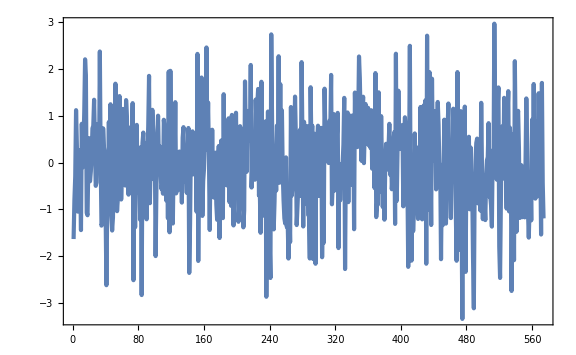

```mathematica
ListPlot[mapx0]
```

### Curvature perturbation PDF

```mathematica
fileNumber="32_0";
DirName="STOLAS_single/data/Starobinsky/";
NmapFileName="Nmap";
CompFileName="compaction";
LogwFileName="logw";
NfileName=DirName<>NmapFileName<>"_"<>fileNumber<>".dat";
CfileName=DirName<>CompFileName<>"_"<>fileNumber<>".dat";
LfileName=DirName<>LogwFileName<>"_"<>fileNumber<>".dat";
```

```mathematica
NMap=Map[#[[2]]&,Sort[Import[NfileName]]];
```

```mathematica
num=Length[NMap]^(1/3)
```

32

```mathematica
NMean=Mean[NMap]
```

21.1621

```mathematica
NVari=Variance[NMap]
```

0.00686095

```mathematica
Skewness[NMap]
Kurtosis[NMap]
```

-0.0232569

2.95675

```mathematica
dN=10 10^-2;
```

```mathematica
histNMap[zz_]:=Select[Flatten[Table[If[zz≤NMap[[cc]]-NMean<zz+dN,NMap[[cc]]-NMean,None],{cc,1,num^3}],2],NumberQ]
```

```mathematica
(*NMapHistList=Select[Table[Ndatas=histNMap[r];If[Length[Ndatas]≥1,{r+dN/2,Length[Ndatas]/(num^3 dN)},None],{r,-5/5,5/5,dN}],Length[#]>1&];*)
```

```mathematica
(*Show[ListLogPlot[NMapHistList,Joined->False],LogPlot[1/Sqrt[2π σ2] Exp[-x^2/(2σ2)]/.{σ2->Variance[NMap]},{x,-1,1}],PlotRange->All]*)
```

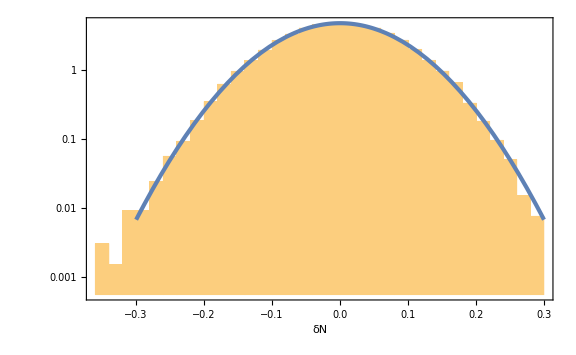

```mathematica
Show[Histogram[NMap-NMean,20,"PDF",ScalingFunctions->"Log",FrameLabel->{"δN",None}],
LogPlot[1/Sqrt[2π σ2] Exp[-x^2/(2σ2)]/.{σ2->Variance[NMap]},{x,-0.3,00.3}](*,
ListLogPlot[NMapHistList,Joined->False,PlotStyle->Red]*),
PlotRange->All]
```

```mathematica
zeta2=Table[If[nx<0,nxt=nx+num,nxt=nx];If[ny<0,nyt=ny+num,nyt=ny];If[nz<0,nzt=nz+num,nzt=nz];NMap[[num^2 nxt+num nyt+nzt+1]]-NMean,{nx,-num/2+1,num/2},{ny,-num/2+1,num/2},{nz,-num/2+1,num/2}];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta2//Flatten]]
```

0.248493

```mathematica
dNFig=ListDensityPlot3D[zeta2,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
ListPlot3D[zeta2[[num/2]],PlotRange->All,BoxRatios->{1, 1, 0.4},Ticks->None,ColorFunction->"Rainbow",PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta+0.1}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

### Curvature perturbation fNL

```mathematica
DirName="chaotic/data/";
NmapFileName="Nmap";
```

```mathematica
datnumber=100;
```

```mathematica
fileNumberList=Table["64_"<>ToString[ll],{ll,0,datnumber-1}];
```

```mathematica
NfileNameList=Table[DirName<>NmapFileName<>"_"<>fileNumberList[[ii]]<>".dat",{ii,datnumber}];
```

```mathematica
fNLList=Table[NMap=Map[#[[2]]&,Sort[Import[NfileNameList[[jj]]]]];
NMean=Mean[NMap];5/18 Mean[Table[(NMap[[nn]]-NMean)^3,{nn,Length[NMap]}]]/(Mean[Table[(NMap[[nn]]-NMean)^2,{nn,Length[NMap]}]]^2),{jj,datnumber}];//AbsoluteTiming
```

{114.504,Null}

```mathematica
Mean[fNLList]±StandardDeviation[fNLList]/(√Length[fNLList])
```

0.0408067±0.0102667

```mathematica
5/6 1/60//N
```

0.0138889

```mathematica
5/12(1-0.9)
```

0.0416667

### Compaction

```mathematica
fileNumber="32_10";
DirName="chaotic/data/";
NmapFileName="Nmap";
CompFileName="compaction";
LogwFileName="logw";
NfileName=DirName<>NmapFileName<>"_"<>fileNumber<>".dat";
CfileName=DirName<>CompFileName<>"_"<>fileNumber<>".dat";
LfileName=DirName<>LogwFileName<>"_"<>fileNumber<>".dat";
```

```mathematica
NMap=Map[#[[2]]&,Sort[Import[NfileName]]];
```

```mathematica
num=Length[NMap]^(1/3)
```

32

```mathematica
NMean=Mean[NMap]
```

30.7009

```mathematica
zeta=Table[NMap[[num^2 (nx-1)+num(ny-1)+nz]]-NMean,{nx,num},{ny,num},{nz,num}];
```

```mathematica
zeta2=Table[If[nx<0,nxt=nx+num,nxt=nx];If[ny<0,nyt=ny+num,nyt=ny];If[nz<0,nzt=nz+num,nzt=nz];NMap[[num^2 nxt+num nyt+nzt+1]]-NMean,{nx,-num/2+1,num/2},{ny,-num/2+1,num/2},{nz,-num/2+1,num/2}];
```

```mathematica
Dzeta=3Sqrt[Variance[zeta//Flatten]]
```

0.615253

```mathematica
dNFig=ListDensityPlot3D[zeta2,BoxRatios->{1, 1, 1},Ticks->None,ColorFunction->(ColorData["TemperatureMap"][(#1/Dzeta+1)/2]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
ListPlot3D[zeta2[[num/2]],BoxRatios->{1, 1, 0.4},Ticks->None,ColorFunction->"TemperatureMap",PlotLegends->BarLegend[{Automatic,{-Dzeta,Dzeta+0.1}},LegendLabel->ζ,LabelStyle->Directive[Large,Black,FontFamily->"Palatino"]],ImageSize->Large]
```

-Graphics3D-

```mathematica
(*Export["chaotic/zeta_32_4.pdf",dNFig];*)
```

```mathematica
dr=1;
Clear[zetardata(*,nxt,nyt,nzt*)]
(*zetardata[r_]:=Select[Flatten[Table[If[(Max[r-dr/2,0])^2<=(i-1)^2+(j-1)^2+(k-1)^2<(r+dr/2)^2,zeta2[[i,j,k]],None],{i,num/2},{j,num/2},{k,num/2}],2],NumberQ]*)
```

```mathematica
zetardata[r_]:=Select[Flatten[Table[If[nx<0,nxt=nx+num,nxt=nx];
If[ny<0,nyt=ny+num,nyt=ny];
If[nz<0,nzt=nz+num,nzt=nz];If[Abs[√(nx^2+ny^2+nz^2)-r]<=dr/2,zeta[[nxt+1,nyt+1,nzt+1]],None],{nx,-num/2+1,num/2},{ny,-num/2+1,num/2},{nz,-num/2+1,num/2}],2],NumberQ]
```

```mathematica
zetarList=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>1,{r,Mean[zetardatas]±StandardDeviation[zetardatas]/Sqrt[Length[zetardatas]]},None],{r,0,num/2-1,dr}],Length[#]>1&];
zetarListwoError=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>=1,{r,Mean[zetardatas]},None],{r,0,num/2-1}],Length[#]>=1&];
```

```mathematica
zetarList
```

{{1,-0.100397±0.021444},{2,-0.0865442±0.0183733},{3,-0.112417±0.0134643},{4,-0.127134±0.0110672},{5,-0.136172±0.00888633},{6,-0.132903±0.00811631},{7,-0.113478±0.0072435},{8,-0.0979519±0.00653411},{9,-0.0825475±0.0054303},{10,-0.0603218±0.00539524},{11,-0.0378206±0.00471235},{12,-0.0252238±0.00430293},{13,-0.0133881±0.00406513},{14,-0.0160229±0.00402865},{15,-0.0129233±0.00408214}}

```mathematica
zetarList=Join[{zetarListwoError[[1]]},zetarList];
```

```mathematica
Nbias=3.5;
```

```mathematica
ksigma[NN_]=(2π σ E^NN)/num/.{σ->10^-1};
```

```mathematica
fit=FindFit[Drop[zetarListwoError,1],A Sin[ksigma[Nbias]r]/(ksigma[Nbias]r),A,r]
```

{A→-0.0936086}

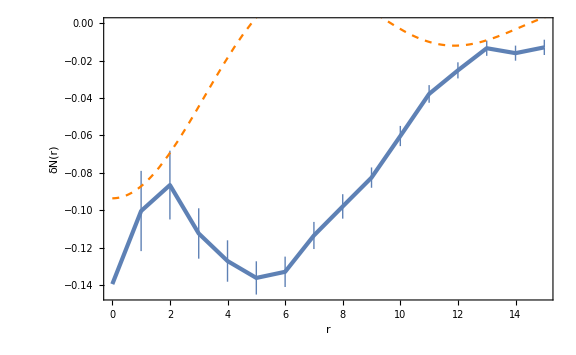

```mathematica
Show[ListPlot[zetarList,FrameLabel->{r,"δN(r)"},PlotLegends->Placed[LineLegend[{"lattice"},LegendMarkerSize->30],{0.8,0.8}](*,PlotRange->{-0.5,5A/.fit}*)],Plot[A Sin[ksigma[Nbias]r]/(ksigma[Nbias]r)/.fit,{r,0,num/2},PlotStyle->{Orange,Dashed},PlotLegends->Placed[LineLegend[{"(sin (SubscriptBox[k, σ] r))/k_σ"},LegendMarkerSize->30],{0.8,0.8}],PlotRange->Full]]
```

```mathematica
zetarint[r_]=Interpolation[zetarListwoError][r];
```

```mathematica
(*dzeta=Join[Table[(zetarListwoError[[ii+2,2]]-zetarListwoError[[ii,2]])/2,{ii,1,num/2-2}],{0}];*)dzeta=Join[{0},Table[(zetarListwoError[[ii+2,2]]-zetarListwoError[[ii,2]])/2,{ii,1,num/2-2}],{0}];
```

```mathematica
CompactionC[r_]=2/3(1-(1+r zetarint'[r])^2);
CompactionD[r_]=2/3(1-(1+r dzeta[[r+1]])^2);//Quiet
```

```mathematica
CDList=Table[{r,CompactionD[r]},{r,0,num/2-1}];
```

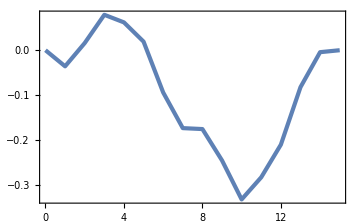

```mathematica
ListPlot[CDList,ImageSize->Medium]
```

```mathematica
CList=Table[{(*ksigma[Nbias]*)r,CompactionC[r]},{r,0,num/2-1}];
```

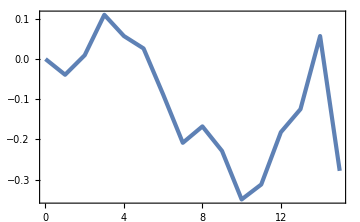

```mathematica
ListPlot[CList,ImageSize->Medium]
```

```mathematica
CompList=Import[CfileName];
```

Import::nffil: Importの最中にファイルchaotic/data/compaction_32_10.datが見付かりませんでした．

```mathematica
ListPlot[CompList,ImageSize->Medium]
```

ListPlot::lpn: $Failedは数値のリストあるいは数値の対のリストではありません．

ListPlot[$Failed,ImageSize→Medium]

ListPlot::lpn: $Failedは数値のリストあるいは数値の対のリストではありません．

Show::gcomb: …のグラフィックスオブジェクトを組み合せることができませんでした．

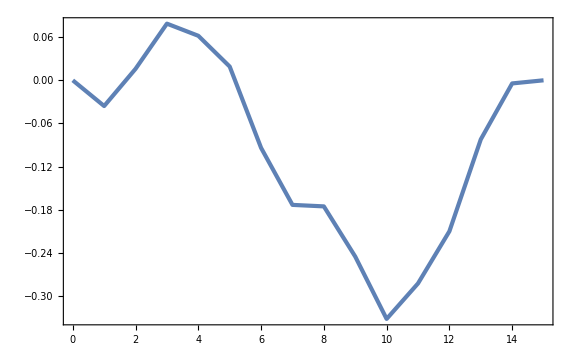
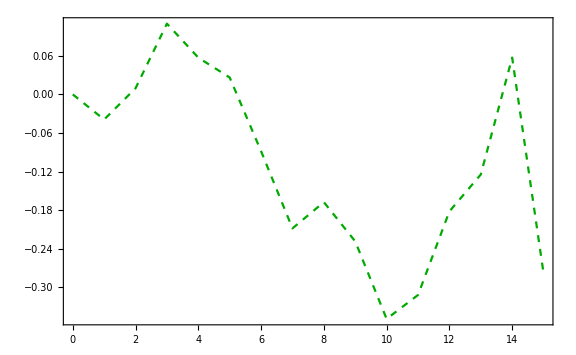
Show[-Graphics-,-Graphics-,ListPlot[$Failed,PlotStyle→{Dashing[{0,Small}],RGBColor[1, 0, 0]}]]

```mathematica
Show[ListPlot[CDList],
ListPlot[CList,PlotStyle->{Dashed,Darker[Green]}],
ListPlot[CompList,PlotStyle->{Dotted,Red}]]
```

```mathematica
(* Continuous averaged compaction function*)
```

```mathematica
CompactionMax=FindMaximum[{CompactionC[r],0<r<num/2-1},{r,num/2-3}];
```

```mathematica
CmpMax=CompactionMax[[1]]
rmax=r/.CompactionMax[[2]]
```

0.0702976

13.7304

```mathematica
Rmax=rmax Exp[zetarint[rmax]]
```

13.5255

```mathematica
NIntegrate[r^2 CompactionC[r] Exp[3zetarint[r]](1+r zetarint'[r]),{r,0,rmax}]/(Rmax^3/3)
```

-0.185151

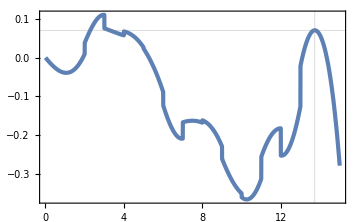

```mathematica
Plot[CompactionC[r],{r,0,num/2-1},GridLines->{{rmax},{CmpMax}},ImageSize->Medium]
```

```mathematica
(** Discretize **)
```

```mathematica
CDList2=Table[CDList[[r,2]],{r,1,num/2}];
```

```mathematica
CmpMaxD=Max[CDList2]
```

0.0787086

```mathematica
rmaxD=Ordering[CDList2,-1][[1]]
```

4

```mathematica
RmaxD=(rmaxD-1) Exp[zetarListwoError[[rmaxD,2]]]
```

2.68102

```mathematica
Sum[(r-1)^2 CDList[[r,2]] Exp[3zetarListwoError[[r,2]]](1+(r-1) dzeta[[r]]),{r,1,rmaxD}]/(RmaxD^3/3)
```

0.0772479

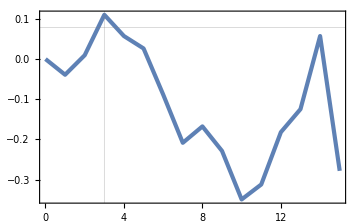

```mathematica
ListPlot[CList,GridLines->{{rmaxD-1},{CmpMaxD}},ImageSize->Medium]
```

```mathematica
Beep[]
```

### Fig1

```mathematica
dr=1;Nbias=3;ksigma[NN_]=(2π σ E^NN)/num/.{σ->10^-1};
```

```mathematica
datnumber=19;
```

```mathematica
DirName="chaotic/data/";
NmapFileName="Nmap";
CompFileName="compaction";
```

```mathematica
fileNumberList=Table["32_"<>ToString[ll],{ll,0,datnumber}];
```

```mathematica
NfileNameList=Table[DirName<>NmapFileName<>"_"<>fileNumberList[[ii]]<>".dat",{ii,datnumber+1}];
(*CfileNameList=Table[DirName<>CompFileName<>"_"<>fileNumberList[[ii]]<>".dat",{ii,datnumber+1}];*)
```

```mathematica
ProbList=Import[DirName<>"probability.dat"];
```

```mathematica
calCA[jj_]:=Module[{},NMap=Map[#[[2]]&,Sort[Import[NfileNameList[[jj]]]]];
CompList=Import[CfileNameList[[jj]]];
num=Length[NMap]^(1/3);
NMean=Mean[NMap];
zeta=Table[NMap[[num^2 (nx-1)+num(ny-1)+nz]]-NMean,{nx,num},{ny,num},{nz,num}];zetardata[r_]:=Select[Flatten[Table[If[nx<0,nxt=nx+num,nxt=nx];
If[ny<0,nyt=ny+num,nyt=ny];
If[nz<0,nzt=nz+num,nzt=nz];If[Abs[√(nx^2+ny^2+nz^2)-r]<=dr/2,zeta[[nxt+1,nyt+1,nzt+1]],None],{nx,-num/2+1,num/2},{ny,-num/2+1,num/2},{nz,-num/2+1,num/2}],2],NumberQ];
zetarListwoError=Select[Table[zetardatas=zetardata[r];If[Length[zetardatas]>=1,{r,Mean[zetardatas]},None],{r,0,num/2-1}],Length[#]>=1&];
fit=A/.FindFit[Drop[zetarListwoError,1],A Sin[ksigma[Nbias]r]/(ksigma[Nbias]r),A,r];
CmAveList=Join[CmAveList,{{fit,ProbList[[jj,3]]}}];
CmList=Join[CmList,{{fit,ProbList[[jj,4]]}}];]
```

```mathematica
CmList={};CmAveList={};
```

```mathematica
Do[calCA[ll],{ll,1,Length[fileNumberList]}]//AbsoluteTiming
```

{107.049,Null}

```mathematica
CmAveList
```

{{0.618968,0.462115},{0.716855,0.407885},{0.650465,0.449709},{0.619339,0.436749},{0.617527,0.439513},{0.670081,0.405635},{0.62315,0.417618},{0.613951,0.444962},{0.654511,0.445911},{0.579151,0.400376},{0.250961,0.325759},{0.393359,0.382972},{0.284218,0.302954},{0.460103,0.35124},{0.342966,0.352342},{0.283131,0.354955},{0.522776,0.456575},{0.147311,0.18621},{0.23575,0.277824},{0.490221,0.402587}}

```mathematica
CmList
```

{{0.618968,0.590191},{0.716855,0.608085},{0.650465,0.613193},{0.619339,0.613899},{0.617527,0.570132},{0.670081,0.607965},{0.62315,0.621361},{0.613951,0.599586},{0.654511,0.623316},{0.579151,0.615502},{0.250961,0.357761},{0.393359,0.454413},{0.284218,0.395751},{0.460103,0.535927},{0.342966,0.403908},{0.283131,0.446357},{0.522776,0.497209},{0.147311,0.265368},{0.23575,0.310828},{0.490221,0.506561}}

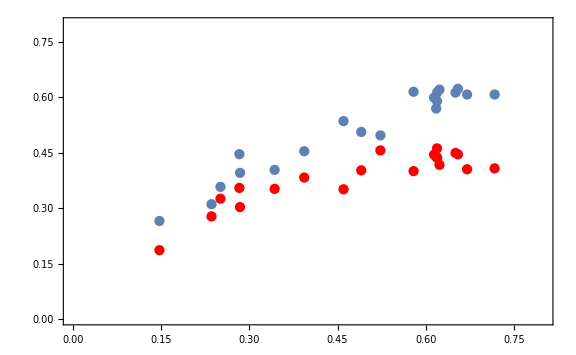

```mathematica
Show[ListPlot[CmList,Joined->False,PlotRange->{{0.,0.8},{0.,0.8}},GridLines->{{},{2/5}}],ListPlot[CmAveList,Joined->False,PlotStyle->Red]]
```

### Power Spectrum

```mathematica
Nkdata=Import["chaotic/data/power_64_119.dat"];
```

```mathematica
ListLogPlot[Nkdata,Joined->False]
```

-Graphics-

```mathematica
cn=0.1;
logn[i_]=i*cn
```

0.1 i

```mathematica
imax=Log[(Length[Nkdata])^(1/3)/2]/cn
```

34.6574

```mathematica
calP[ii_]:=Total[Select[Table[If[Abs[logn[ii]-Log[Nkdata[[i,1]]]]<=cn/2,Nkdata[[i,2]],None],{i,1,Length[Nkdata]}],Positive]]*1/cn
```

```mathematica
calP[ii_]:=Total[Select[Table[If[Abs[cn ii-Log[Nkdata[[i,1]]]]<=cn/2,Nkdata[[i,2]],None],{i,1,Length[Nkdata]}],Positive]]*1/cn
```

```mathematica
power=ParallelTable[{Exp[logn[i]],calP[i]},{i,0,imax}];//AbsoluteTiming(*cn=0.1でmaxn=35,cn=0.01でmaxn=332*)
```

{5.38777,Null}

```mathematica
calPklin=Import["chaotic/data/calPlin_chaotic.dat"]//ToExpression;
```

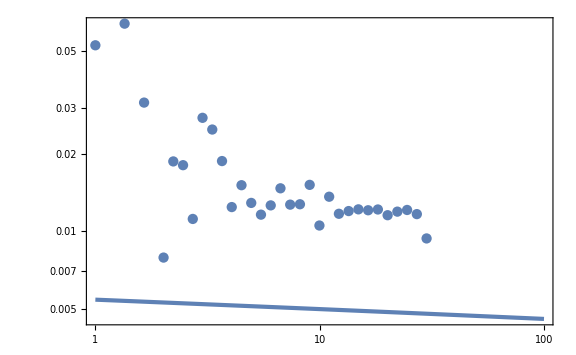

```mathematica
Show[ListLogLogPlot[power,Joined->False],ListLogLogPlot[calPklin],PlotRange->All]
```

### Averaged Power Spectrum

```mathematica
calPkdisc=Import["chaotic/data/powers.dat"];
```

```mathematica
calPave=Table[0,{ii,Length[Drop[calPkdisc[[1]],1]]}];
Do[calPave+=Drop[calPkdisc[[ii]],1],{ii,Length[calPkdisc]}]
```

```mathematica
calPave
```

{10.2651,0,0,5.81424,0,1.88493,0,1.07405,2.42724,1.85854,0.64084,1.22962,1.79543,1.49208,1.34765,1.33927,1.29294,1.14725,1.14192,1.31568,1.33279,1.22705,1.46057,1.08005,1.32608,1.16996,1.16881,1.19872,1.19609,1.18798,1.14723,1.16624,1.16845,1.14012,0.931063}

```mathematica
cn=0.1;
logn[i_]=(i-1)*cn;
```

```mathematica
calPkAve=Table[{Exp[logn[i]],calPave[[i]]/Length[calPkdisc]},{i,Length[Drop[calPkdisc[[1]],1]]-1}];
```

```mathematica
calPklin=Import["chaotic/data/calPlin_chaotic.dat"]//ToExpression;
```

```mathematica
calPklinMod=Table[{calPklin[[nn,1]],5/6 calPklin[[nn,2]]},{nn,Length[calPklin]}];
```

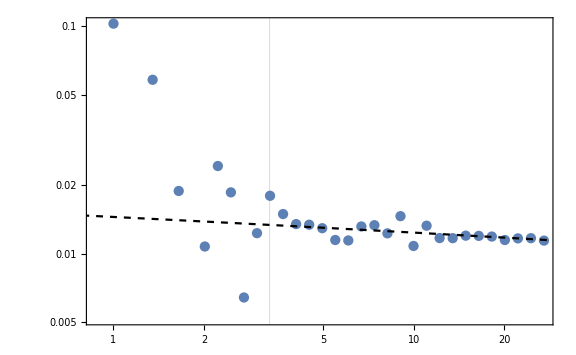

```mathematica
Show[ListLogLogPlot[calPkAve,Joined->False,GridLines->{{0.1 ⅇ^3.5},None}],ListLogLogPlot[calPklinMod,PlotStyle->{Dashed,Black}]]
```

```mathematica
PlotList[k_]:=ListLogPlot[Drop[calPkdisc[[k]],1],Joined->False,PlotStyle->Hue[k/Length[calPkdisc]]]
```

```mathematica
PList=Table[{PlotList[k]},{k,Length[calPkdisc]}];
```

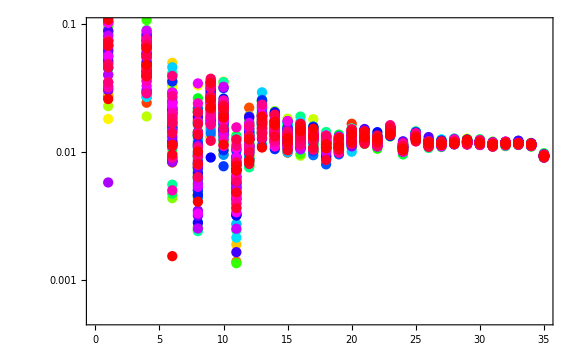

```mathematica
Show[ListLogPlot[calPave/Length[calPkdisc],Joined->False,PlotMarkers->{"OpenMarkers",Large},PlotRange->{Automatic,{0.0005,0.1}}],PList]
```

### PDF

```mathematica
DirName="chaotic/data/";
PDFFileName0=DirName<>"probabilities0.dat";
PDFFileName1=DirName<>"probabilities1.dat";
PDFFileName2=DirName<>"probabilities2.dat";
PDFFileName3=DirName<>"probabilities3.dat";
```

```mathematica
CompactionPDF=Join[Import[PDFFileName0],Import[PDFFileName1],Import[PDFFileName2],Import[PDFFileName3]];
```

```mathematica
clength=Length[CompactionPDF];
```

```mathematica
logw=Table[CompactionPDF[[ii,2]],{ii,1,clength}];
```

```mathematica
weight=Table[Exp[CompactionPDF[[ii,2]]],{ii,1,clength}];
```

```mathematica
Cint=Table[CompactionPDF[[ii,3]],{ii,1,clength}];
```

```mathematica
Cmax=Table[CompactionPDF[[ii,4]],{ii,1,clength}];
```

```mathematica
Select[CompactionPDF,#[[2]]<-50&]
```

{{93,-52.1327,0.378528,0.564447,6.48697,6},{119,-56.3341,0.433733,0.620078,8.95016,9},{466,-52.106,0.444488,0.637836,9.99054,10},{662,-50.0253,0.398144,0.663689,9.08332,9}}

```mathematica
Mean[weight*Cint]
```

0.0000350666

```mathematica
Mean[weight*Cmax]
```

0.0000451254

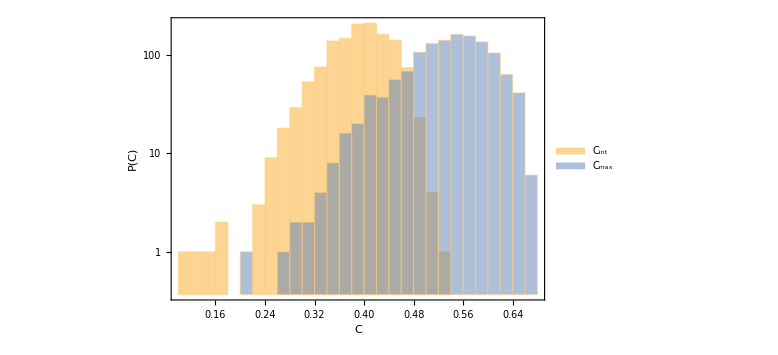

```mathematica
Show[Histogram[{Cint,Cmax},ScalingFunctions-> "Log",ChartLegends->{"C_int","C_max"}],PlotRange->All,Frame->True,FrameLabel->{"C","P(C)"}]
```

```mathematica
dc=10 10^-3;
```

```mathematica
histCintdata[c_]:=Select[Flatten[Table[If[c<Cint[[cc]]≤c+dc,Cint[[cc]],None],{cc,1,clength}],2],NumberQ]
```

```mathematica
histWintdata[c_]:=Select[Flatten[Table[If[c<Cint[[cc]]≤c+dc,weight[[cc]],None],{cc,1,clength}],2],NumberQ]
```

```mathematica
histlogwintdata[c_]:=Select[Flatten[Table[If[c<Cint[[cc]]≤c+dc,logw[[cc]],None],{cc,1,clength}],2],NumberQ]
```

```mathematica
histCmaxdata[c_]:=Select[Flatten[Table[If[c<Cmax[[cc]]≤c+dc,Cmax[[cc]],None],{cc,1,clength}],2],NumberQ]
```

```mathematica
histWmaxdata[c_]:=Select[Flatten[Table[If[c<Cmax[[cc]]≤c+dc,weight[[cc]],None],{cc,1,clength}],2],NumberQ]
```

```mathematica
histlogwmaxdata[c_]:=Select[Flatten[Table[If[c<Cmax[[cc]]≤c+dc,logw[[cc]],None],{cc,1,clength}],2],NumberQ]
```

```mathematica
CintListNW=Select[Table[cintdatas=histCintdata[r];weightdatas=histWintdata[r];If[Length[cintdatas]>1,{r+dc,Length[cintdatas]/(clength dc)},None],{r,0,50 10^-2,dc}],Length[#]>1&];
```

```mathematica
CmaxListNW=Select[Table[cmaxdatas=histCmaxdata[r];weightdatas=histWmaxdata[r];If[Length[cmaxdatas]>1,{r+dc,Length[cmaxdatas]/(clength dc)},None],{r,0,80 10^-2,dc}],Length[#]>1&];
```

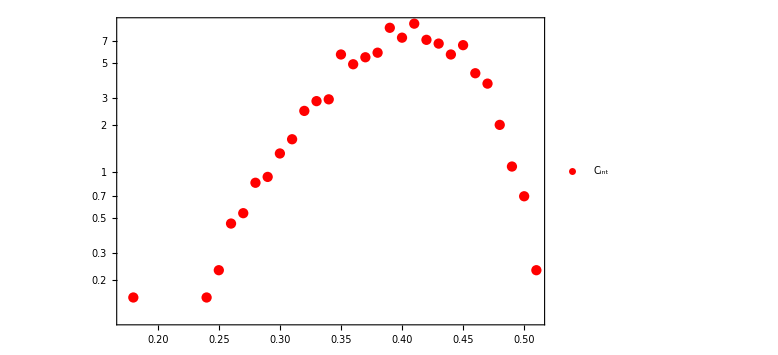

```mathematica
ListLogPlot[CintListNW,Joined->False,PlotStyle->Red,PlotLegends->Placed[LineLegend[{"C_int"},LegendMarkerSize->30],{0.9,0.9}]]
```

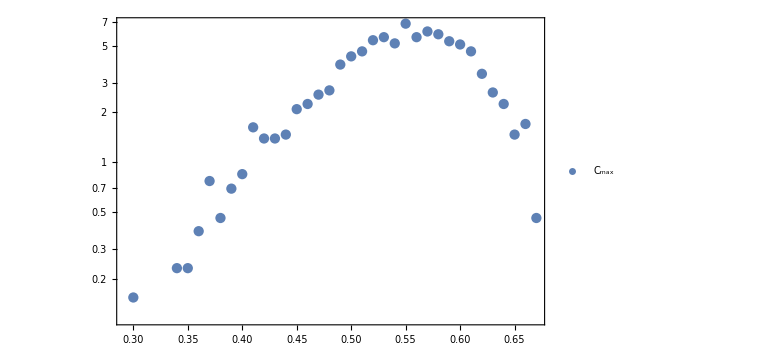

```mathematica
ListLogPlot[CmaxListNW,Joined->False,PlotLegends->Placed[LineLegend[{"C_max"},LegendMarkerSize->30],{0.9,0.9}]]
```

```mathematica
CintList=Select[Table[cdatas=histCintdata[r];weightdatas=histWintdata[r];logwdatas=histlogwintdata[r];ProbC=Length[cdatas]/(clength dc)Total[weightdatas];ϵpm[p_]:=Abs[Exp[(-1)^p √(StandardDeviation[logwdatas]^2/Length[cdatas]+StandardDeviation[logwdatas]^4/(2Length[cdatas]-2))]-1];If[Length[cdatas]>1,{r+dc,Around[ProbC,{ProbC ϵpm[1],ProbC ϵpm[0]}]},None],{r,0,50 10^-2,dc}],Length[#]>1&];
```

```mathematica
CmaxList=Select[Table[cdatas=histCmaxdata[r];weightdatas=histWmaxdata[r];logwdatas=histlogwmaxdata[r];ProbC=Length[cdatas]/(clength dc)Total[weightdatas];ϵpm[p_]:=Abs[Exp[(-1)^p √(StandardDeviation[logwdatas]^2/Length[cdatas]+StandardDeviation[logwdatas]^4/(2Length[cdatas]-2))]-1];If[Length[cdatas]>1,{r+dc,Around[ProbC,{ProbC ϵpm[1],ProbC ϵpm[0]}]},None],{r,0,80 10^-2,dc}],Length[#]>1&];
```

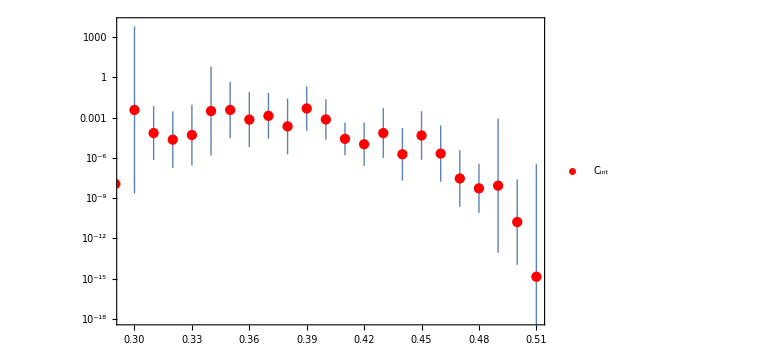

```mathematica
ListLogPlot[CintList,PlotRange->{{0.295,Automatic},{10^-18,10^4}},Joined->False,PlotStyle->Red,PlotLegends->Placed[LineLegend[{"C_int"},LegendMarkerSize->30],{0.9,0.9}]]
```

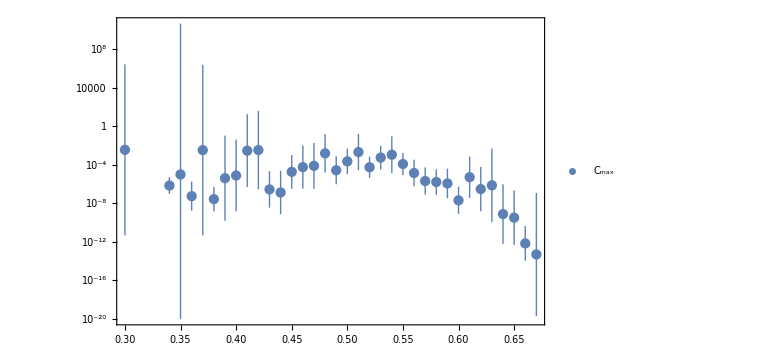

```mathematica
Show[ListLogPlot[CmaxList,Joined->False,PlotLegends->Placed[LineLegend[{"C_max"},LegendMarkerSize->30],{0.9,0.9}]],PlotRange->All]
```

```mathematica
WCbar=Table[{CompactionPDF[[ii,3]],Log[Exp[CompactionPDF[[ii,2]]]]},{ii,1,clength}];
```

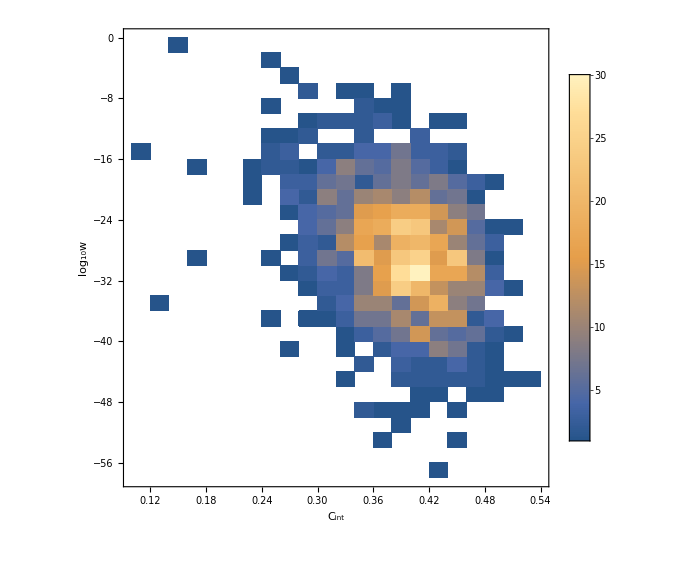

```mathematica
DensityHistogram[WCbar,20,FrameLabel->{"C_int","log_10w"},ChartLegends->Automatic,AspectRatio->1]
```

### Mass function

```mathematica
ParametersMass={K3->1,γ->36 10^-2,Cth->2/5,MassScale->10^20,HReentry->156 10^11 Mpc^-1};
```

```mathematica
LatticeSize=1/64 10^-12 Mpc;
```

```mathematica
PBHlist=Select[CompactionPDF,#[[3]]>Cth/.ParametersMass&];
```

```mathematica
PBHlength=Length[PBHlist]
```

613

```mathematica
logwPBH=Table[PBHlist[[ii,2]],{ii,1,PBHlength}];
```

```mathematica
CintPBH=Table[PBHlist[[ii,3]],{ii,1,PBHlength}];
```

```mathematica
RmaxPBH=Table[PBHlist[[ii,5]],{ii,1,PBHlength}];
```

```mathematica
Mass[c_,r_]:=K3(c-Cth)^γ(MassScale(r^-1/HReentry)^-2)/.ParametersMass(** Kitajima, et al eq.(2.22) **)
```

```mathematica
PBHMass=Table[10^-20 Mass[CintPBH[[i]],LatticeSize RmaxPBH[[i]]],{i,PBHlength}]//Simplify;
```

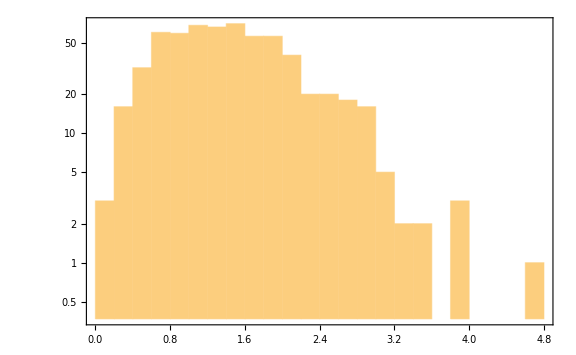

```mathematica
Histogram[PBHMass,ScalingFunctions->"Log"]
```

```mathematica
(*HistogramList[PBHMass]*)
```

```mathematica
dM=20 10^-2(*MassScale/.ParametersMass*);
```

```mathematica
MassList=Table[10^-1(1+dM)^cc,{cc,1,36}];MassList//N
```

{0.12,0.144,0.1728,0.20736,0.248832,0.298598,0.358318,0.429982,0.515978,0.619174,0.743008,0.89161,1.06993,1.28392,1.5407,1.84884,2.21861,2.66233,3.1948,3.83376,4.60051,5.52061,6.62474,7.94968,9.53962,11.4475,13.7371,16.4845,19.7814,23.7376,28.4852,34.1822,41.0186,49.2224,59.0668,70.8802}

```mathematica
histMassPBH[MM_]:=Select[Flatten[Table[If[MM<PBHMass[[cc]]≤MM(1+dM),PBHMass[[cc]],None],{cc,1,PBHlength}],2],NumberQ]
```

```mathematica
histWintPBH[MM_]:=Select[Flatten[Table[If[MM<PBHMass[[cc]]≤MM(1+dM),logwPBH[[cc]],None],{cc,1,PBHlength}],2],NumberQ]
```

```mathematica
histRmaxPBH[MM_]:=Select[Flatten[Table[If[MM<PBHMass[[cc]]≤MM(1+dM),RmaxPBH[[cc]],None],{cc,1,PBHlength}],2],NumberQ]
```

```mathematica
CintPBHListNW=Select[Table[Massdatas=histMassPBH[MassList[[mm]]];ProbM=Length[Massdatas]/(clength (MassList[[mm+1]] -MassList[[mm]]));If[Length[Massdatas]≥1,{MassList[[mm]],ProbM},None],{mm,1,Length[MassList]-1}],Length[#]>1&];
```

```mathematica
CintPBHListNW//N
```

{{0.12,0.032175},{0.144,0.0268125},{0.1728,0.0446875},{0.20736,0.0186198},{0.248832,0.0775825},{0.298598,0.0646521},{0.358318,0.0862028},{0.429982,0.0897946},{0.515978,0.179589},{0.619174,0.205779},{0.743008,0.239037},{0.89161,0.251162},{1.06993,0.238171},{1.28392,0.264634},{1.5407,0.268142},{1.84884,0.148272},{2.21861,0.0783126},{2.66233,0.0493079},{3.1948,0.00483411},{3.83376,0.00302132},{4.60051,0.000839255}}

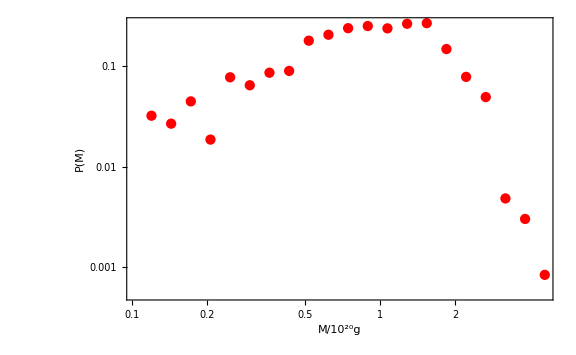

```mathematica
ListLogLogPlot[CintPBHListNW,Joined->False,PlotStyle->Red,FrameLabel->{"M/10^20g","P(M)"}]
```

```mathematica
MassPBHList=Select[Table[Massdatas=histMassPBH[MassList[[mm]]];logwdatas=histWintPBH[MassList[[mm]]];ProbC=Length[Massdatas]/(clength (MassList[[mm+1]] -MassList[[mm]]))Exp[Mean[logwdatas]+Variance[logwdatas]/2];ϵpm[p_]:=Abs[Exp[(-1)^p √(StandardDeviation[logwdatas]^2/Length[Massdatas]+StandardDeviation[logwdatas]^4/(2Length[Massdatas]-2))]-1];If[Length[Massdatas]>1,{MassList[[mm]],Around[ProbC,{ProbC ϵpm[1],ProbC ϵpm[0]}]},None],{mm,1,Length[MassList]-1}],Length[#]>1&];
```

Variance::shlen: 引数{-20.1671}は少なくとも2つの要素を持っていなければなりません．

Variance::shlen: 引数{-29.3753}は少なくとも2つの要素を持っていなければなりません．

Variance::shlen: 引数{-13.9732}は少なくとも2つの要素を持っていなければなりません．

General::stop: この計算中に，Variance::shlenのこれ以上の出力は表示されません．

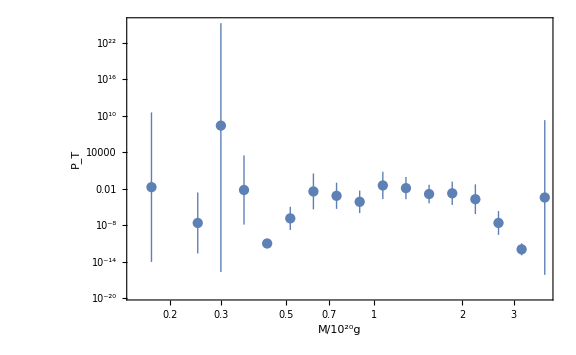

```mathematica
ListLogLogPlot[MassPBHList,PlotRange->All(*{{0.3,2.5},{10^-21,10^-1}}*),Joined->False,FrameLabel->{"M/10^20g","P_T"},GridLines->{{},{10^-9}}]
```

```mathematica
fPBHList=Table[{MassPBHList[[nn,1]],MassPBHList[[nn,1]]/(6.62 10^-13)MassPBHList[[nn,2]]},{nn,1,Length[MassPBHList]}];
```

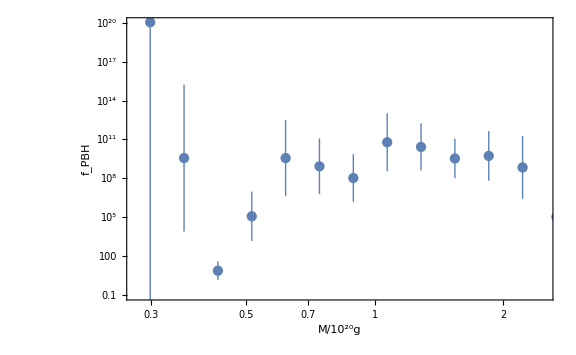

```mathematica
ListLogLogPlot[fPBHList,PlotRange->{{0.275,2.5},{10^-1,10^20}},Joined->False,FrameLabel->{"M/10^20g","f_PBH"},GridLines->{{},{10^4}}]
```

```mathematica
WCbar=Table[{10^-20 Mass[CintPBH[[i]],LatticeSize RmaxPBH[[i]]],Log10[Exp[logwPBH[[i]]]]},{i,1,PBHlength}];
```

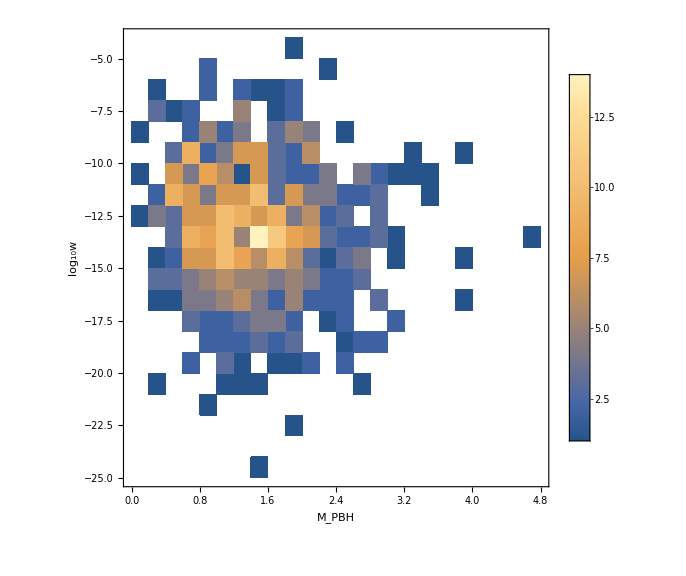

```mathematica
DensityHistogram[WCbar,20,FrameLabel->{"M_PBH","log_10w"},ChartLegends->Automatic,AspectRatio->1]
```